```mathematica
ClearAll;
Off[NIntegrate::ncvb]
Off[NIntegrate::precw]
Off[NIntegrate::slwcon]
Off[Root::npoly]
SetDirectory[NotebookDirectory[]];
On[Assert]
```

## Set Parameters

```mathematica
wkpc = 20; (*working precision*)
MaxOrder = 30; (*highest order of basis used *)
xdetector = 0.3 (*cm*);
m=7/2;
mh = 7/2;
ξmaxn3 = 1.119935;   (*Subscript[ξ, max] for n = 3*)
ξmaxn0 = 1.231173;  (*Subscript[ξ, max] for n = 0*)
ξmaxn72 = 1.1110443;  (*Subscript[ξ, max] for n = 7/2*)
T0val = 0.4;
ρ0val = 0.1134;
ZZ =4.5;
κ0val = 0.088*ZZ^2*0.4^(-7/2)* ρ0val;
cv0val = 10;
stdDrive = 0.1 * T0val;
stdDensity = 0.1 * ρ0val;
NPn = 12;
NHe=12;
tval = 0.6
pval = 0.1;
Nevalpoints = 200;
omegaval =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->mh, a-> 0.01372, c -> 299.98 };
omegavaln0 =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->0, a-> 0.01372, c -> 299.98 };
omegafunc[a_,c_, n_]:= 2 Sqrt[(2a c)]/Sqrt[3(n+4)];
δH = 0.5;
DrivePars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->0, a3->0, a4->0,ω->omegaval};
DriveParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive , a2->0, a3->0, a4->0,ω->omegaval};
DensityPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->0.1*ρ0val, a4->0,ω->omegaval};
BothPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval*T0val, a2->0, a3->pval*ρ0val, a4->0,ω->omegaval};
BothParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive, a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
DensityParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
transfer ={Subscript[a, 1]->a1, Subscript[a, 3]->a3,Subscript[a, 4]->a4,Subscript[a, 2]->a2, ρ̄->ρ0, OverBar[Subscript[c, v]]->cv, κ̄->κ0, T̄->T0, n->mh, ξ->ξmaxn72, ω->omegaval};
AllPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
TargetPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
```

0.6

```mathematica
|
```

## Some lists

```mathematica
FactorialList = Table[Factorial[j],{j,0,NHe}];
LegendreList = Table[1/(2 j+ 1),{j,0, NPn}];
```

## Useful functions

```mathematica
analyticDriveProfile[x_,t_, pars_, k_] := 1/2 NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0]^k,{xx1, -1,1}]
analyticTargetProfile[x_,t_, pars_, k_] := 1/8 NIntegrate[IntegrandFunc2[x,t,pars, 0, xx2,xx3, xx4]^k,{xx2, -1,1},{xx3,-1,1},{xx4,-1,1}, WorkingPrecision->14]
analyticAllProfile[x_,t_, pars_, k_] := 1/16 NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2,xx3, xx4]^k,{xx1,-1,1},{xx2, -1,1},{xx3,-1,1},{xx4,-1,1}]
analyticDriveProfileHe[x_,t_, pars_, k_] := 1/Sqrt[2Pi] NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0]^k Exp[-xx1^2/2],{xx1, -∞,∞}, WorkingPrecision->14, PrecisionGoal->10]
analyticTargetProfileHe[x_,t_, pars_, k_] := (1/Sqrt[2 Pi])^3NIntegrate[IntegrandFunc2[x,t,pars, 0, xx2,xx3, xx4]^k Exp[-xx2^2/2] Exp[-xx3^2/2] Exp[-xx4^2/2],{xx2, -∞,∞},{xx3,-∞,∞},{xx4,-∞,∞}]
analyticAllProfileHe[x_,t_, pars_, k_] := (1/Sqrt[2 Pi])^4NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2,xx3, xx4]^k Exp[-xx1^2/2]Exp[-xx2^2/2] Exp[-xx3^2/2] Exp[-xx4^2/2],{xx2, -∞,∞},{xx1, -∞,∞},{xx3,-∞,∞},{xx4,-∞,∞}]
percentilefuncPn[samples_, resolution_]:=Module[{ medianallpn = Table[0,{j,1, Nevalpointspython}], twentiethallpn = Table[0,{j,1, Nevalpointspython}], eightiethallpn= Table[0,{j,1, Nevalpointspython}], histdist = Table[HistogramDistribution[samples[[j]],{resolution}], {j, 1, Nevalpointspython}]},
For[ix = 1, ix<= Nevalpointspython, ix++,
medianallpn[[ix]] = {xlistpython[[ix]],MakeICDF[samples[[ix]], 0.5, resolution, histdist[[ix]]]};
If[medianallpn[[ix]][[2]] >medianallpn[[1]][[2]], medianallpn[[ix]][[2]] = 0]]
For[ix = 1, ix<= Nevalpointspython, ix++,
twentiethallpn[[ix]] = {xlistpython[[ix]],MakeICDF[samples[[ix]], 0.2, resolution,histdist[[ix]]]};
If[twentiethallpn[[ix]][[2]] >twentiethallpn[[1]][[2]] || twentiethallpn[[ix]]<0, twentiethallpn[[ix]][[2]] = 0]];
For[ix = 1, ix<= Nevalpointspython, ix++,
eightiethallpn[[ix]] = {xlistpython[[ix]],MakeICDF[samples[[ix]], 0.8, resolution, histdist[[ix]]]};
If[eightiethallpn[[ix]][[2]] >eightiethallpn[[1]][[2]], eightiethallpn[[ix]][[2]] = 0]];
{medianallpn, twentiethallpn,eightiethallpn }]
percentilefuncHe[samples_, resolution_]:=Module[{ medianallpn = Table[0,{j,1, Nevalpointspython}], twentiethallpn = Table[0,{j,1, Nevalpointspython}], eightiethallpn= Table[0,{j,1, Nevalpointspython}]},
For[ix = 1, ix<= Nevalpointspython, ix++,
medianallpn[[ix]] = {xlistpythonh[[ix]],MakeICDF[samples[[ix]], 0.5, resolution]};
If[medianallpn[[ix]][[2]] >medianallpn[[1]][[2]], medianallpn[[ix]][[2]] = 0]]
For[ix = 1, ix<= Nevalpointspython, ix++,
twentiethallpn[[ix]] = {xlistpythonh[[ix]],MakeICDF[samples[[ix]], 0.2, resolution]};
If[twentiethallpn[[ix]][[2]] >twentiethallpn[[1]][[2]], twentiethallpn[[ix]][[2]] = 0]];
For[ix = 1, ix<= Nevalpointspython, ix++,
eightiethallpn[[ix]] = {xlistpythonh[[ix]],MakeICDF[samples[[ix]], 0.8, resolution]};
If[eightiethallpn[[ix]][[2]] >eightiethallpn[[1]][[2]], eightiethallpn[[ix]][[2]] = 0]];
{medianallpn, twentiethallpn,eightiethallpn }]
MakeICDF[samples_, quart_, res_, dist_]:=Module[{icdf=InverseCDF[dist,x]} ,icdf/.x->quart]
T0funcU[x_, pars_]:=( T0 + a1 x)/.pars
analyticProfileDriveUncertainty[x_,t_, pars_] := 1/2 NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0],{xx1, -1,1}, WorkingPrecision->14]
ξfunc[AA_, x_, t_] := AA x/Sqrt[t] 
IntegrandFunc2[x_,t_,pars_, x1_, x2_, x3_, x4_] := Tsol2[ξfunc[AAfunc[pars, x1, x2, x3, x4],x, t]] * T0funcU[x1, pars]
RMSE[data1_, data2_]:= Sqrt[Mean[(data1-data2)^2]]
AAfunc[ pars_,x1_, x2_, x3_, x4_]:= Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(mh)]  / ω/.pars;
tempNthMomentPn[x_,t_, pars_, k_] := 1/16 NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k,{xx1,-1,1},{xx2, -1,1},{xx3, -1,1},{xx4,-1,1}, PrecisionGoal->12]
tempNthMomentHe[x_,t_, pars_, k_] := 1/(4 Pi^2)NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k Exp[-xx1^2/2]Exp[-xx2^2/2]Exp[-xx3^2/2]Exp[-xx4^2/2],{xx1,-∞,∞},{xx2, -∞,∞},{xx3, -∞,∞},{xx4,-∞,∞}, WorkingPrecision->14]
analyticprofileDriveHe[x_,t_, pars_] := 1/Sqrt[2 Pi] NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0] Exp[-xx1^2/2],{xx1,-∞,∞}, WorkingPrecision->14]
sobol[SAMPLES_, dim_]:=BlockRandom[SeedRandom[Method->{"MKL",Method->{"Sobol","Dimension"->dim}}];
RandomReal[1,{SAMPLES,dim}]];
Basis[n_,x_] := LegendreP[n,x]
HBasis[nnn_, x_] := FullSimplify[(-1)^(nnn) Exp[xx^2/2] D[Exp[-xx^2/2],{xx,nnn}]/.xx->x];
BreakoutTime[θ1_, θ2_, θ3_, θ4_, pars_, xdet_]:=  (xdet^2/(ξ^2 ω^2))(T̄ + a1 θ1)^(-(n))(κ̄ + a2_ θ2)^1(ρ̄ + a3 θ3)^2(OverBar[Subscript[c, v]] + a4_ θ4)^1/.{T̄->T0,ρ̄->ρ0,OverBar[Subscript[c, v]] ->cv,κ̄ ->κ0 }/.pars
(*functions to calculate expansion of the breakout time*)
g1func[x_, pars_,n_]:= 1/(ξ^2 ω^2) (T0 + a1 x)^(-n)/.pars;
g2func[x_,pars_]:= (κ0 + a2 x)^(1)/.pars;
g3func[x_,pars_]:= (ρ0 + a3 x)^(2)/.pars;
g4func[x_,pars_] := (cv + a4 x)^(1)/.pars 
G1func[n_,pars_,nn_, bound_]:= (2n + 1)/2 NIntegrate[g1func[ x,pars,nn] Basis[n,x], {x, -bound,bound}, WorkingPrecision->2*wkpc, AccuracyGoal->18]
G2func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g2func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G3func[n_,pars_, bound_]:= (2n + 1)/2 NIntegrate[g3func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G4func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g4func[ x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
HG1func[n_,pars_,nn_, bound_]:=1/(Sqrt[2 Pi] Factorial[n])NIntegrate[(g1func[ z,pars,nn]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, (*Exclusions->z==  N[-T0/a1/.pars]*)WorkingPrecision->wkpc, AccuracyGoal->15]
HG2func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g2func[ z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG3func[n_,pars_, bound_]:=1/(Sqrt[2 Pi] Factorial[n]) NIntegrate[( g3func[ z,pars]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG4func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g4func[z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
g1coeffs[M_,pars_,nn_,b_] := Table[G1func[n,pars,nn, b],{n,0,M}]
g2coeffs[M_,pars_, b_] := Table[G2func[n,pars, b],{n,0,M}]
g3coeffs[M_,pars_, b_] := Table[G3func[n,pars, b],{n,0,M}]
g4coeffs[M_,pars_, b_] := Table[G4func[n,pars, b],{n,0,M}]
h1coeffs[M_,pars_,nn_,b_] := Table[HG1func[ni, pars,nn, b],{ni,0,M}]
h2coeffs[M_,pars_, b_] := Table[HG2func[ni,pars, b],{ni,0,M}]
h3coeffs[M_,pars_, b_] := Table[HG3func[ni,pars, b],{ni,0,M}]
h4coeffs[M_,pars_, b_] := Table[HG4func[ni,pars, b],{ni,0,M}]
MakeCoeffsG[NN_, pars_, m_]:= {g1coeffs[NN,pars,m,1], g2coeffs[NN, pars,1],g3coeffs[NN, pars,1],g4coeffs[NN, pars,1] }
MakeCoeffsH[NN_, pars_, m_]:= {h1coeffs[NN,pars,m,1], h2coeffs[NN, pars,1],h3coeffs[NN, pars,1],h4coeffs[NN, pars,1] }
BasisList = Table[Basis[j,x],{j,0,MaxOrder}];
BasisListF[n_,xx_] := BasisList[[n+1]]/.x->xx
expansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[ParallelTable[coeffs[[1]][[n]]Basis[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]Basis[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]Basis[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]Basis[n-1,x4],{n,1,NN+1}]]
HBasisList = Table[HBasis[j,x],{j,0,MaxOrder}];
HBasisListF[n_,xx_] := HBasisList[[n+1]]/.x->xx
Hexpansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[Table[coeffs[[1]][[n]]HBasisListF[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]HBasisListF[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]HBasisListF[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]HBasisListF[n-1,x4],{n,1,NN+1}]]
(*Functions to calculate moments of the 1d expansions*) 
MakeExpPn[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeExpHe[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeSecondMomentHe[nn_, coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]]
MakeVarPn[nn_,coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2LegendreList[[1;;nn]]] - MakeExpPn[coeffs]^2
MakeVarHe[nn_,coeffs_]:= xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]] - (MakeExpHe[coeffs])^2
MakeSkewPn[nn_, coeffs_]:= (1/16 xdetector^6ThirdMoment[nn, TripleProdLeg, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[4]][[1;;nn]]] - 3 MakeExpPn[coeffs]MakeVarPn[nn, coeffs] -MakeExpPn[coeffs]^3) /(MakeVarPn[nn, coeffs]^(3/2))
MakeSkewHe[nn_, coeffs_]:= ( xdetector^6ThirdMoment[nn, TripleProdHe, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[4]][[1;;nn]]] - 3 MakeExpHe[coeffs]MakeVarHe[nn, coeffs] -MakeExpHe[coeffs]^3) /(MakeVarHe[nn, coeffs]^(3/2))
MakeKurtPn[nn_, coeffs_]:= (1/16 xdetector^8FourthMoment[nn, QuadrupleProdLeg, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[4]][[1;;nn]]] - 6(MakeVarPn[nn,coeffs]+MakeExpPn[coeffs]^2)MakeExpPn[coeffs]^2 - 3 MakeExpPn[coeffs]^4)/ MakeVarPn[nn, coeffs]^2
MakeKurtHe[nn_, coeffs_]:= (xdetector^8FourthMoment[nn, QuadrupleProdHe, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[4]][[1;;nn]]] - 6(MakeSecondMomentHe[nn,coeffs])MakeExpHe[coeffs]^2 - 3 MakeExpHe[coeffs]^4)/ MakeVarHe[nn, coeffs]^2
ThirdMoment[nn_,AAA_, coeffs_]:= Total[Total[Total[Table[AAA[[i]][[j]][[k]]coeffs[[i]]coeffs[[j]]coeffs[[k]],{i,1,nn}, {j,1,nn},{k,1,nn}]]]]
(*ThirdMoment[nn_,AAA_, coeffs_]:= Integrate[Total[Total[Total[]]],{x,-1,1}]*)
FourthMoment[nn_,AAA_, coeffs_]:=Total[ Total[Total[Total[Table[AAA[[i]][[j]][[k]][[n]]coeffs[[i]]coeffs[[j]]coeffs[[k]]coeffs[[n]],{i,1,nn}, {j,1,nn},{k,1,nn},{n,1,nn}]]]]]
```

## Expensive tensors that can be loaded

```mathematica
TripleProdHeFunc[i_,j_,k_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i || Abs[j-k]>i || (EvenQ[j+k]&& OddQ[i ]|| OddQ[j+k]&&EvenQ[i]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]Exp[-x^2/2],{x,-∞,∞}]]
QuadrupleProdHeFunc[i_,j_,k_,m_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i +m|| Abs[j-k]>i+m || (EvenQ[j+k]&& OddQ[i+m ]|| OddQ[j+k]&&EvenQ[i+m]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]HBasis[m,x]Exp[-x^2/2],{x,-∞,∞}]]
```

```mathematica
(*TripleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn}];
TripleProdHe = ParallelTable[TripleProdHeFunc[i,j,k],{i,0,NHe},{j,0,NHe}, {k,0,NHe}];*)
```

```mathematica
(*QuadrupleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x]Basis[n,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn},{n,0,NPn}];*)
```

```mathematica
(*QuadrupleProdHe =ParallelTable[QuadrupleProdHeFunc[i,j,k,n],{i,0,NHe},{j,0,NHe},{k,0,NHe},{n,0,NHe}];*)
```

```mathematica
(*Export["triple_prod_leg.hdf",TripleProdLeg];
Export["triple_prod_he.hdf",TripleProdHe];
Export["quadruple_prod_leg.hdf",QuadrupleProdLeg];
Export["quadruple_prod_he.hdf",QuadrupleProdHe];*)
TripleProdLeg2=Rationalize[Import["triple_prod_leg.hdf",{"Datasets","Dataset1"}]];
TripleProdHe2=Rationalize[Import["triple_prod_he.hdf",{"Datasets","Dataset1"}]];
QuadrupleProdLeg2=Rationalize[Import["quadruple_prod_leg.hdf",{"Datasets","Dataset1"}]];
QuadrupleProdHe2=Rationalize[Import["quadruple_prod_he.hdf",{"Datasets","Dataset1"}]];
Assert[Total[Total[Total[TripleProdLeg2-TripleProdLeg ]]]==0]
Assert[Total[Total[Total[TripleProdHe2-TripleProdHe ]]]==0]
Assert[Total[Total[Total[Total[QuadrupleProdLeg2-QuadrupleProdLeg ]]]]==0]
Assert[Total[Total[Total[Total[QuadrupleProdHe2-QuadrupleProdHe ]]]]==0]
TripleProdLeg = TripleProdLeg2;
TripleProdHe = TripleProdHe2;
QuadrupleProdLeg = QuadrupleProdLeg2;
QuadrupleProdHe = QuadrupleProdHe2;
```

## Analytic solutions

```mathematica
DriveBkoutnthMomentPn[n2_]:= 1/2((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2)^n2 ((-a1^2+T0^2)^(-mh n2) (-(-a1+T0)^(mh n2) (a1+T0)+(-a1+T0) (a1+T0)^(mh n2)))/(a1 (-1+mh n2)) (* nth moment of a URV drive uncertainty*)
AllBkoutnthMomentPn[n2_]:=-((((xdetector^2 (T0-Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2 (-T0+Subscript[a, 1])+(T0+Subscript[a, 1]) ((xdetector^2 (T0+Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2) (-(κ0-Subscript[a, 2])^(1+n2)+(κ0+Subscript[a, 2])^(1+n2)) (-(ρ0-Subscript[a, 3])^(1+2 n2)+(ρ0+Subscript[a, 3])^(1+2 n2)) (-(cv-Subscript[a, 4])^(1+n2)+(cv+Subscript[a, 4])^(1+n2)))/(16 (1+n2)^2 (1+2 n2) (-1+n n2) Subscript[a, 1] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4]) (* nth moment of a URV all uncertain*)
DriveBkoutnthMomentHe[n2_, pars_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  (* nth moment of a NRV drive uncertain*)
DriveBkoutnthMomentHeSing[n2_, pars_, δH_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,-δH-(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,δH+(T0/a1/.DrivePars),∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"] (* nth moment of a URV all uncertain, tries to avoid the singularity*)
HeBreakoutIntegrand[pars_,θ1_,θ2_,θ3_,θ4_,n2_]:=1/Sqrt[2 Pi]^4((( ρ0+Subscript[a, 3] θ3)^2 (cv+Subscript[a, 4] θ4)(κ0+Subscript[a, 2] θ2))/(ξ^2ω^2)(Subscript[a, 1] θ1+T0)^(-n )xdetector^2/.transfer/.pars)^n2 Exp[-θ1^2/2]Exp[-θ2^2/2]Exp[-θ3^2/2]Exp[-θ4^2/2]/.transfer/.pars/.n->mh
AllBkoutnthMomentHe[n2_, pars_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-∞,∞},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  
AllBkoutnthMomentHeSing[n2_, pars_, δH_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.pars)},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->12, PrecisionGoal->12, Method->"GlobalAdaptive"]  
(*These calculate the moment based statistics of Subscript[t, b] for uncertain drive*)
 varExact = (DriveBkoutnthMomentPn[2] - DriveBkoutnthMomentPn[1]^2)/.DrivePars;
varExactHe = (DriveBkoutnthMomentHe[2, DrivePars] - DriveBkoutnthMomentHe[1, DrivePars]^2);
skewExact = (DriveBkoutnthMomentPn[3] - 3 DriveBkoutnthMomentPn[1]varExact - DriveBkoutnthMomentPn[1]^3)/varExact^(3/2)/.DrivePars;
skewExactHe = (DriveBkoutnthMomentHeSing[3,DrivePars,δH] - 3 DriveBkoutnthMomentHe[1, DrivePars]varExactHe - DriveBkoutnthMomentHe[1, DrivePars]^3)/varExactHe^(3/2);
kurtExact = (DriveBkoutnthMomentPn[4] - 6 DriveBkoutnthMomentPn[2]DriveBkoutnthMomentPn[1]^2 -3 DriveBkoutnthMomentPn[1]^4)/varExact^(2)/.DrivePars;
kurtExactHe = 1/varExactHe^(2)(DriveBkoutnthMomentHeSing[4,DrivePars,δH] - 6 DriveBkoutnthMomentHe[2, DrivePars]DriveBkoutnthMomentHe[1, DrivePars]^2 -3 DriveBkoutnthMomentHe[1,DrivePars]^4)/.DrivePars;
(*These calculate the moment based statistics of Subscript[t, b] for all parameters uncertain *)
varExactAll = (AllBkoutnthMomentPn[2] - AllBkoutnthMomentPn[1]^2)/.transfer/.AllPars;
varExactHeAll = (AllBkoutnthMomentHe[2, AllPars] - AllBkoutnthMomentHe[1, AllPars]^2);
skewExactAll = (AllBkoutnthMomentPn[3] - 3 AllBkoutnthMomentPn[1]varExactAll - AllBkoutnthMomentPn[1]^3)/varExactAll^(3/2)/.transfer/.AllPars;

kurtExactAll = (AllBkoutnthMomentPn[4] - 6 AllBkoutnthMomentPn[2]AllBkoutnthMomentPn[1]^2 -3 AllBkoutnthMomentPn[1]^4)/varExactAll^(2)/.transfer/.AllPars;
δH = 0.5;
firstmom =AllBkoutnthMomentHeSing[1, AllPars, δH];
skewExactHeAll = (AllBkoutnthMomentHeSing[3,AllPars, δH] - 3firstmom varExactHeAll - firstmom^3)/varExactHeAll^(3/2);
kurtExactHeAll = 1/varExactHeAll^(2)(AllBkoutnthMomentHeSing[4,AllPars, δH] - 6AllBkoutnthMomentHe[2, AllPars]firstmom^2 -3 firstmom^4)/.AllPars;
```

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

```mathematica
..
```

## Breakout time convergence

```mathematica
(*calculate 1d coefficients and export to python*)
NN = 14; (*order of the basis *)
drivecoeffs = MakeCoeffsG[NN, DrivePars, mh];
targetcoeffs = MakeCoeffsG[NN, TargetPars, mh];
bothcoeffs = MakeCoeffsG[NN, BothPars, mh];
allcoeffs = MakeCoeffsG[NN, AllPars, mh];
drivecoeffsH = MakeCoeffsH[NN, DrivePars, mh];
targetcoeffsH = MakeCoeffsH[NN, TargetPars, mh];
bothcoeffsH = MakeCoeffsH[NN, BothPars, mh];
allcoeffsH = MakeCoeffsH[NN, AllPars, mh];
Export["drivecoeffs.csv", drivecoeffs];
Export["targetcoeffs.csv", targetcoeffs];
Export["allcoeffs.csv", allcoeffs];
Export["drivecoeffs_he.csv", Re[drivecoeffsH]];
Export["targetcoeffs_he.csv", Re[targetcoeffsH]];
Export["allcoeffs_he.csv", Re[allcoeffsH]];
```

$Aborted

$Aborted

```mathematica
(*Drive uncertainty*)
```

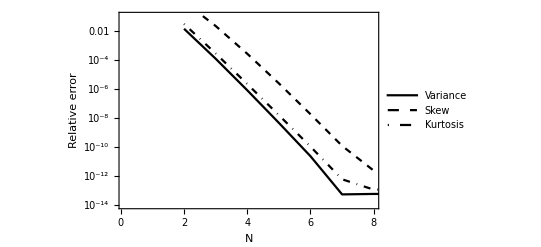

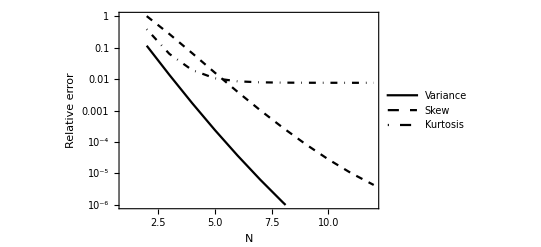

```mathematica
ERR = Table[0, {k,0,3},{j,NPn-1}];
ERRHe = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,drivecoeffs[[;;]]];
skewtest = MakeSkewPn[nn, drivecoeffs[[;;]]];
kurttest = MakeKurtPn[nn,drivecoeffs[[;;]]] ;
ERR[[1]][[nn-1]] = {nn,Abs[(vartest - varExact)]/varExact};
ERR[[2]][[nn-1]]={nn,Abs[(skewtest - skewExact)]/skewExact};
ERR[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExact)]/Abs[kurtExact] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,drivecoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, drivecoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,drivecoeffsH[[;;]]] ;
ERRHe[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHe)]/Abs[varExactHe]};
ERRHe[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHe)]/Abs[skewExactHe]};
ERRHe[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHe)]/Abs[kurtExactHe] };
]
styles=Flatten@Table[{Directive[color],Directive[Dashed,color, Thick],Directive[DotDashed,color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
drivePnConvergence = ListLogPlot[{ERR[[1]], ERR[[2]], ERR[[3]]}, Joined->True, PlotRange->{{0.1, NPn-4},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
driveHeConvergence = ListLogPlot[{ERRHe[[1]], ERRHe[[2]], ERRHe[[3]]}, Joined->True, PlotRange->{{1, 12},{10^(-6),1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
(*All uncertainty*)
```

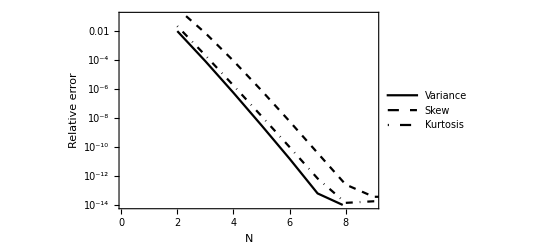

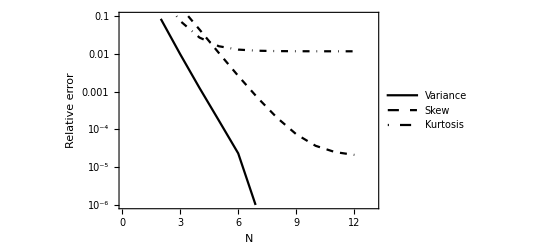

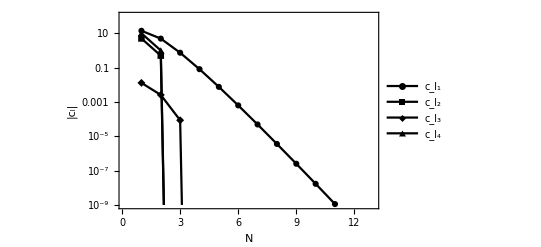

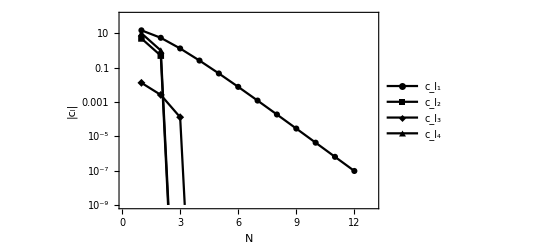

```mathematica
ERRAll = Table[0, {k,0,3},{j,NPn-1}];
ERRHeAll = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,allcoeffs[[;;]]];
skewtest = MakeSkewPn[nn, allcoeffs[[;;]]];
kurttest = MakeKurtPn[nn,allcoeffs[[;;]]] ;
ERRAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactAll)]/varExactAll};
ERRAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactAll)]/skewExactAll};
ERRAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactAll)]/Abs[kurtExactAll] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,allcoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, allcoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,allcoeffsH[[;;]]] ;
ERRHeAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHeAll)]/varExactHeAll};
ERRHeAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHeAll)]/skewExactHeAll};
ERRHeAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHeAll)]/Abs[kurtExactHeAll] };
]
AllPnConvergence = ListLogPlot[{ERRAll[[1]], ERRAll[[2]], ERRAll[[3]]}, Joined->True, PlotRange->{{0.1, NPn-3},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
AllHeConvergence = ListLogPlot[{Re[ERRHeAll[[1]][[1;;6]]], ERRHeAll[[2]], ERRHeAll[[3]]}, Joined->True, PlotRange->{{0.1, NHe+1},{10^(-6),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
styles2=Flatten@Table[{Directive[color],Directive[color],Directive[color],Directive[color]},{color,{Black,Gray}} ];
CoeffsAllPnPlot = ListLogPlot[{ Table[{j, Abs[allcoeffs[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[3]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
CoeffsAllHePlot = ListLogPlot[{ Table[{j, Abs[allcoeffsH[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[3]][[j]]]},{j,0,NHe+1}], Table[{j, Abs[allcoeffsH[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
(*Export[ "UQ_plots/drivePnConverge.pdf",drivePnConvergence]*)
(*Export[ "UQ_plots/driveHeConverge.pdf",driveHeConvergence]*)
(*Export[ "UQ_plots/AllPnConverge_10.pdf",AllPnConvergence]*)
(*Export[ "UQ_plots/AllHeConverge.pdf",AllHeConvergence]*)
(*Export["UQ_plots/CoeffsAllUncertainPn_10.pdf",CoeffsAllPnPlot]*)
(*Export["UQ_plots/CoeffsAllUncertainHe_10.pdf",CoeffsAllHePlot]*)
```

```mathematica
Print["Expected Pn ", MakeExpPn[allcoeffs]]
Print["Expected He ", MakeExpHe[allcoeffsH]]
```

Expected Pn 0.813972

Expected He 0.867198

## Histogram plots of breakout time

```mathematica
(*Load results from python*)
```

```mathematica
heresults =Import["he_samples.hdf5", "results"];
pnresults =Import["pn_samples.hdf5", "results"];
Hsamples = heresults[[1]];
Hdensitysamples= heresults[[2]];
Hallsamples = heresults[[3]];
samples = pnresults[[1]];
densitysamples= pnresults[[2]];
allsamples = pnresults[[3]];
```

```mathematica
xmin = Min[allsamples];
xmax = Max[allsamples];
mean = Mean[allsamples];
std = Sqrt[Variance[allsamples]];
median = Median[allsamples];
nominal = expansion[0,0,0,0, allcoeffs, NN] * xdetector^2;
lineStyle={Thick,Red,Dashed};
maxy = 100;
line1=Line[{{median,-20},{median,maxy}}];
line2 = Line[{{mean,-20},{mean,maxy}}];
line3 = Line[{{nominal,-20},{nominal,maxy}}];
(*line4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
line5 = Line[{{mean- std, 0.4}, {mean+std, 0.4}}];
line6 = Line[{{mean - std, -20}, {mean-std, 20}}];
𝒟= HistogramDistribution[samples];
𝒟2= HistogramDistribution[densitysamples, {0.01}];
(*𝒟3= HistogramDistribution[combinedsamples, {0.01}];*)
(*𝒟4 =  HistogramDistribution[DirectSampleBothParsU, {0.01}];*)
𝒟5 =  HistogramDistribution[allsamples, {0.01}];
styles3=Flatten@Table[{Directive[Dashed,color, Thick],Directive[Dotted,color, Thick],Directive[color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
shiftδ = 10^{-8}*0;
(*PDF PN*)
( DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,3.6}},Epilog->{Black, line1, Text[Rotate[Style["median value",Black,Bold, Medium],-90 Degree],{median + .01,1.25}],Black,DotDashed,line2,Text[Rotate[Style["mean value",Black,Bold, Medium],-90 Degree],{mean+.01,1.25}],Black,Dashed, line3, Text[Rotate[Style["nominal value",Black,Bold, Medium],-90 Degree],{nominal-.01,1.25}], Black,Dashing[None], line5, Text[Style["1-σ",Black,Bold, Medium],{0.7,0.45}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF})[[1]]
```

ParallelTable::iterb: Iterator {n,1,1+NN} does not have appropriate bounds.

ParallelTable::nopar1: ParallelTable[allcoeffs⟦1⟧⟦n⟧ Basis[n-1,0],{n,1,1+NN}] cannot be parallelized; proceeding with sequential evaluation.

Table::iterb: Iterator {n,1,1+NN} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

HistogramDistribution::invldd: The input data HistogramDistribution[samples] should be a vector or a matrix of real numbers or a valid TemporalData object.

HistogramDistribution::invldd: The input data HistogramDistribution[densitysamples] should be a vector or a matrix of real numbers or a valid TemporalData object.

HistogramDistribution::invldd: The input data HistogramDistribution[allsamples] should be a vector or a matrix of real numbers or a valid TemporalData object.

-Graphics-

```mathematica
𝒟5N =  HistogramDistribution[allsamples, {0.00001}];
percentilelist = {.20,.40,.50,.60,.80};
twentieth = InverseCDF[𝒟5N,0.2];
eightieth= InverseCDF[𝒟5N,0.8];
fiftieth = InverseCDF[𝒟5N,0.5];
nominalcdf = CDF[𝒟5N,nominal];
meancdf = CDF[𝒟5N,mean];
For[n =1,n<= 5, n++,Print[NumberForm[InverseCDF[𝒟5N,percentilelist[[n]]],6]," ", percentilelist[[n]]," percentile"]]
```

0.63078 0.2 percentile

0.733865 0.4 percentile

0.78712 0.5 percentile

0.845111 0.6 percentile

0.989323 0.8 percentile

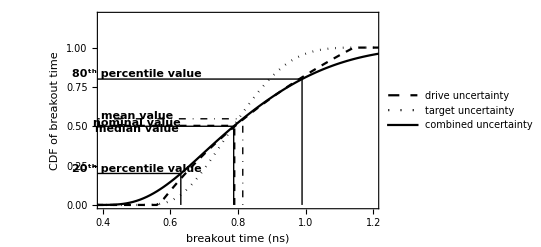

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
(*CDF PN*)
(DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.2}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black,Bold, Medium],{0.5,0.48}], Text[Style["nominal value",Black,Bold, Medium],{0.5,0.52}], Text[Style["mean value",Black,Bold, Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black,Bold, Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black,Bold, Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF})[[1]]
```

```mathematica
(*Export["UQ_plots/histogramPDF_PN.pdf", plot1];
Export["UQ_plots/histogramCDF_PN.pdf", plot2];*)
```

```mathematica
(*PDF and CDF He*)
```

```mathematica
Hline1=Line[{{medianH,-20},{medianH,20}}];
Hline2 = Line[{{meanH,-20},{meanH,maxy}}];
Hline3 = Line[{{nominalH,-20},{nominalH,maxy}}];
(*Hline4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
Hline5 = Line[{{meanH- stdH, 0.25}, {meanH+stdH, 0.25}}];
Hline6 = Line[{{meanH - stdH, -20}, {meanH-stdH, 20}}];
medianH = Median[Hallsamples];
meanH = Mean[Hallsamples]
varH = Variance[Hallsamples];
stdH = Sqrt[varH];
nominalH = Re[Hexpansion[0,0,0,0, allcoeffsH, NN] * xdetector^2];
maxy = 100;
ℋ= HistogramDistribution[Hsamples, {0.01}];
ℋ2= HistogramDistribution[Hdensitysamples, {0.01}];
ℋ5 =  HistogramDistribution[Hallsamples, {0.01}];
ℋ5N = HistogramDistribution[Hallsamples, {0.00001}];
```

0.867139

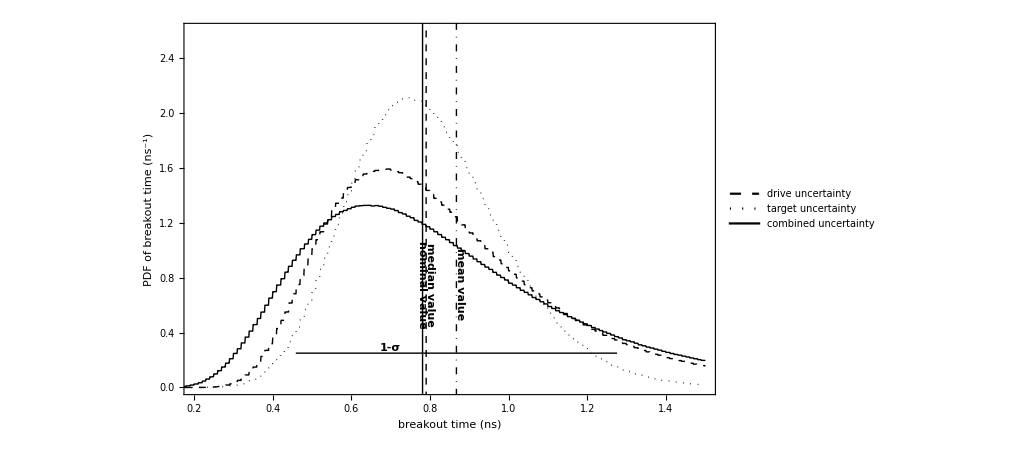

```mathematica
(DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.2, 1.5},{0,2.6}},Epilog->{Black, Hline1, Text[Rotate[Style["median value",Black, Bold, Medium],-90 Degree],{medianH + .02,.75}],Black,DotDashed,Hline2,Text[Rotate[Style["mean value",Black,Bold,  Medium],-90 Degree],{meanH+.01,.75}],Black,Dashed, Hline3, Text[Rotate[Style["nominal value",Black, Bold, Medium],-90 Degree],{nominalH-.01,.75}], Black,Dashing[None], Hline5, Text[Style["1-σ",Black, Bold, Medium],{0.7,0.29}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF})[[1]]
```

```mathematica
twentieth = InverseCDF[ℋ5N,0.2];
eightieth= InverseCDF[ℋ5N,0.8];
fiftieth = InverseCDF[ℋ5N,0.5];
nominalcdf = CDF[ℋ5N,nominal]
meancdf = CDF[ℋ5N,mean];
For[n =1,n<= 5, n++,Print[NumberForm[InverseCDF[ℋ5N,percentilelist[[n]]],6]," ", percentilelist[[n]]," percentile"]]
```

0.510876

0.547715 0.2 percentile

0.701153 0.4 percentile

0.780994 0.5 percentile

0.870961 0.6 percentile

1.12766 0.8 percentile

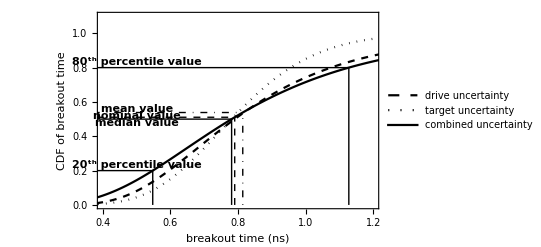

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];         
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
(DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.1}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black,Bold,  Medium],{0.5,0.48}], Text[Style["nominal value",Black,Bold,  Medium],{0.5,0.52}], Text[Style["mean value",Black,Bold,  Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black,Bold,  Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black,Bold,  Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF})[[1]]
```

```mathematica
(*Export["UQ_plots/histogramPDF_HE.pdf", plot3];
Export["UQ_plots/histogramCDF_HE.pdf", plot4];*)
```

## Temperature profile

```mathematica
(*Find min and max Subscript[ξ, max]*)
nm = 7/2;
xmaxmin =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,-1, 1, 1, 1];
xmaxmax =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,1, -1, -1, -1];
xmaxmaxhe =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,1.5, -1.5, -1.5, -1.5];
xlist = N@Subdivide[0,xmaxmax,Nevalpoints];
(*Export parameters to python code*)
AllParsCsv =  N[{T0val, ξmaxn72, κ0val, ρ0val,cv0val,pval* T0val,pval*κ0val, pval*ρ0val, pval*cv0val,omegaval, NPn, NHe, mh, tval, xmaxmax, 300, xmaxmaxhe}];
Export["marshak_pars.csv", AllParsCsv];
```

```mathematica
pval* T0val
```

pval T0val

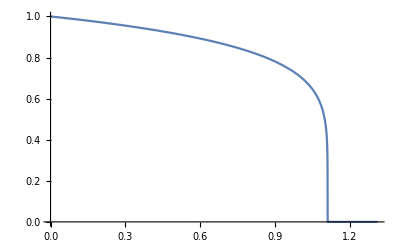

```mathematica
(*Analytic T solutions*)
(*solve Marshak wave*)
(*load Marshak wave*)
marshakxi= Import["marshak_sol.hdf5",{"Datasets","xi"}];
marshakT= Import["marshak_sol.hdf5",{"Datasets","T"}];
interpolationlist = Table[0,{j,1, Length[marshakT]}];
For[it = 1, it<= Length[marshakT], it++,
interpolationlist[[it]] = {marshakxi[[it]], marshakT[[it]]};]
Ts = Interpolation[interpolationlist];
(*ICS[ξmax_, ξ_] := {T[ξmax]==1/5((nm+3)*ξmax*(-ξ+ξmax)/(nm+4))^(1/(nm+3)), u[ξmax]==-(((nm+3)/(nm+4))*ξmax)^(1/(nm+3))*1/(nm+3)*(ξmax-ξ)^((-2-nm)/(nm+3))1/5}
eqsMarshak = {D[T[ξ],ξ]==u[ξ], D[u[ξ],ξ] ==- u[ξ]*((T[ξ]^(-mh)*ξ)/(nm+4)+(nm+3)*T[ξ]^2*u[ξ])/(T[ξ]^3)} ;
bcs = {T[0]==1};
tol = 10^-7;
sol=NDSolve[{eqsMarshak,ICS[ξmaxn72,ξmaxn72-tol]},{T[ξ],u[ξ]},{ξ,0,ξmaxn72-tol},Method->{"Shooting","StartingInitialConditions"->{T[ξmaxn72]==ICS[ξmaxn72,ξmaxn72-tol][[1]],u[ξmaxn72]==ICS[ξmaxn72,ξmaxn72-tol][[2]]}}];*)
Clear[Tsol2]
(*Tsol2[ξξ_?NumericQ] :=Piecewise[{{((T[ξ]/.sol)/.ξ->ξξ )[[1]],0<=ξξ<=ξmaxn72},{0,True}}]*)
Tsol2[ξξ_?NumericQ] :=Piecewise[{{((Ts[ξ])/.ξ->ξξ ),0<=ξξ<=ξmaxn72},{0,True}}]
Plot[{ Tsol2[x]},{x,0,ξmaxn72 + 0.2}]
```

```mathematica
(*Import coefficients from python*)
AllPnCC= Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_all_pn.hdf5",{"Datasets","all_Pn"}];
DrivePnCC=Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_drive_pn.hdf5",{"Datasets","drive_Pn"}];
TargetPnCC=Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_target_pn.hdf5",{"Datasets","target_Pn"}];
AllHeCC= Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_all_he.hdf5",{"Datasets","all_He"}];
DriveHeCC=Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_drive_he.hdf5",{"Datasets","drive_He"}];
TargetHeCC=Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_target_he.hdf5",{"Datasets","target_He"}];
xlistpython = Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_drive_pn.hdf5",{"Datasets","xlist"}];
xlistpythonh = Import["/Users/bennett/Documents/GitHub/PCE_UQ/coeffs_4d_drive_he.hdf5",{"Datasets","xlist"}];
Nevalpointspython = Length[xlistpython];
```

```mathematica
expansionfunc[coeffs_, NN_,x_]:= Total[Total[Total[Total[Table[coeffs[[i,j,k,l]]Basis[i-1,x]Basis[0,x]Basis[0,x]Basis[0,x],{i,1,NN},{j,1,NN},{k,1,NN},{l,1,NN}]]]]]
expansionfunc1d[coeffs_, NN_,x_]:= Total[Table[coeffs[[i,1,1,1]]Basis[i-1,x],{i,1,NN}]]
expansionfunc1dH[coeffs_, NN_,x_]:= Total[Table[coeffs[[i,1,1,1]]HBasis[i-1,x],{i,1,NN}]]
```

```mathematica
dataIntegrand
```

{{{-1,-0.0673427},{-24/25,-0.0580647},{-23/25,-0.0487866},{-22/25,-0.0395085},{-21/25,-0.0302305},{-4/5,-0.0209524},{-19/25,-0.0116744},{-18/25,-0.00239633},{-17/25,0.00688172},{-16/25,0.0161598},{-3/5,0.0254378},{-14/25,0.0347159},{-13/25,0.0439939},{-12/25,0.053272},{-11/25,0.0625501},{-2/5,0.0718281},{-9/25,0.0811062},{-8/25,0.0903842},{-7/25,0.0996623},{-6/25,0.10894},{-1/5,0.118218},{-4/25,0.127496},{-3/25,0.136774},{-2/25,0.146053},{-1/25,0.155331},{0,0.164609},{1/25,0.173887},{2/25,0.183165},{3/25,0.192443},{4/25,0.201721},{1/5,0.210999},{6/25,0.220277},{7/25,0.229555},{8/25,0.238833},{9/25,0.248111},{2/5,0.257389},{11/25,0.266667},{12/25,0.275945},{13/25,0.285223},{14/25,0.294501},{3/5,0.303779},{16/25,0.313058},{17/25,0.322336},{18/25,0.331614},{19/25,0.340892},{4/5,0.35017},{21/25,0.359448},{22/25,0.368726},{23/25,0.378004},{24/25,0.387282},{1,0.39656}},{{-1,0.023712},{-24/25,0.0112027},{-23/25,0.000958238},{-22/25,-0.00711747},{-21/25,-0.0131207},{-4/5,-0.0171475},{-19/25,-0.0192943},{-18/25,-0.0196572},{-17/25,-0.0183324},{-16/25,-0.0154161},{-3/5,-0.0110045},{-14/25,-0.00519377},{-13/25,0.00191981},{-12/25,0.0102401},{-11/25,0.0196708},{-2/5,0.0301159},{-9/25,0.041479},{-8/25,0.053664},{-7/25,0.0665746},{-6/25,0.0801147},{-1/5,0.0941881},{-4/25,0.108699},{-3/25,0.12355},{-2/25,0.138646},{-1/25,0.15389},{0,0.169187},{1/25,0.18444},{2/25,0.199552},{3/25,0.214428},{4/25,0.228972},{1/5,0.243087},{6/25,0.256677},{7/25,0.269646},{8/25,0.281897},{9/25,0.293335},{2/5,0.303863},{11/25,0.313385},{12/25,0.321805},{13/25,0.329026},{14/25,0.334953},{3/5,0.339489},{16/25,0.342538},{17/25,0.344004},{18/25,0.343791},{19/25,0.341802},{4/5,0.337941},{21/25,0.332112},{22/25,0.324219},{23/25,0.314165},{24/25,0.301855},{1,0.287192}},{{-1,-0.0121732,0.0218237},{-24/25,-0.00474789,-0.00258054},{-23/25,0.00193323,-0.0101877},{-22/25,0.00671631,-0.00815111},{-21/25,0.00905994,-0.00186626},{-4/5,0.0088977,0.00487783},{-19/25,0.00651691,0.00970357},{-18/25,0.0024525,0.0114225},{-17/25,-0.00260456,0.00980085},{-16/25,-0.00788519,0.0053248},{-3/5,-0.0126074,-0.00102416},{-14/25,-0.0160296,-0.00797612},{-13/25,-0.0174922,-0.0141558},{-12/25,-0.0164498,-0.0182372},{-11/25,-0.0124932,-0.0190679},{-2/5,-0.00536246,-0.0157608},{-9/25,0.00504674,-0.00775462},{-8/25,0.0186851,0.00515691},{-7/25,0.0353572,0.0228237},{-6/25,0.0547345,0.0447632},{-1/5,0.0763728,0.070206},{-4/25,0.0997341,0.0981583},{-3/25,0.12421,0.127477},{-2/25,0.14915,0.156949},{-1/25,0.173886,0.185382},{0,0.197764,0.211678},{1/25,0.220169,0.234912},{2/25,0.240553,0.254393},{3/25,0.25846,0.26971},{4/25,0.273546,0.280757},{1/5,0.285599,0.28774},{6/25,0.294552,0.291159},{7/25,0.300489,0.291767},{8/25,0.303651,0.290506},{9/25,0.304429,0.288424},{2/5,0.303351,0.286578},{11/25,0.301064,0.28592},{12/25,0.298296,0.287195},{13/25,0.295827,0.290827},{14/25,0.294423,0.296841},{3/5,0.294785,0.304812},{16/25,0.297465,0.31386},{17/25,0.302777,0.322725},{18/25,0.310693,0.329926},{19/25,0.320727,0.334037},{4/5,0.331793,0.334117},{21/25,0.342056,0.330308},{22/25,0.348764,0.32465},{23/25,0.348054,0.322144},{24/25,0.334749,0.332113},{1,0.302128,0.3699}},{{-1,0.},{-24/25,0.},{-23/25,0.},{-22/25,0.},{-21/25,0.},{-4/5,0.},{-19/25,0.},{-18/25,0.},{-17/25,0.},{-16/25,0.},{-3/5,0.},{-14/25,0.},{-13/25,0.},{-12/25,0.},{-11/25,0.},{-2/5,0.},{-9/25,0.},{-8/25,0.},{-7/25,0.},{-6/25,0.},{-1/5,0.},{-4/25,0.144672},{-3/25,0.191619},{-2/25,0.211046},{-1/25,0.224282},{0,0.234597},{1/25,0.243187},{2/25,0.25063},{3/25,0.257251},{4/25,0.263253},{1/5,0.268771},{6/25,0.273901},{7/25,0.27871},{8/25,0.283252},{9/25,0.287566},{2/5,0.291684},{11/25,0.295631},{12/25,0.299429},{13/25,0.303094},{14/25,0.306641},{3/5,0.310082},{16/25,0.313427},{17/25,0.316686},{18/25,0.319865},{19/25,0.322972},{4/5,0.326013},{21/25,0.328993},{22/25,0.331916},{23/25,0.334787},{24/25,0.337609},{1,0.340385}}}

```mathematica
dataIntegrand=Transpose@Table[{{x,expansionfunc1d[DrivePnCC[[200]],2,x ]},{x,expansionfunc1d[DrivePnCC[[200]],4,x ]},{x,expansionfunc1d[DrivePnCC[[200]],8,x ]},{x,expansionfunc1d[DrivePnCC[[200]],10,x ] },{x,Tsol2[ ξfunc[AAfunc[DrivePars,x , 0, 0, 0], xlistpython[[200]],tval]](T0val+T0val/10 x)}},{x,Subdivide[-1,1,40]}];
dataIntegrand3 = Transpose@Table[,{x,Subdivide[-1,1,50]}];
styles6=Flatten@Table[{Directive[ color, Thick],Directive[ color, Thick],Directive[ color, Thick],Directive[ color, Thick],Directive[ color, Thick],Directive[color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];plotwaveexpansion = ListPlot[dataIntegrand,Frame->{True, True, False, False},FrameLabel->{Style["θ_1", Large],Style["T_0(θ_1)T̃(θ_1)", Large]},PlotStyle->styles6, PlotLegends->{"M=1", "M=3", "M = 5", "M = 7", "M=9"}, Joined->True, PlotMarkers->{"OpenMarkers","OpenMarkers", "OpenMarkers","OpenMarkers",None}]
```

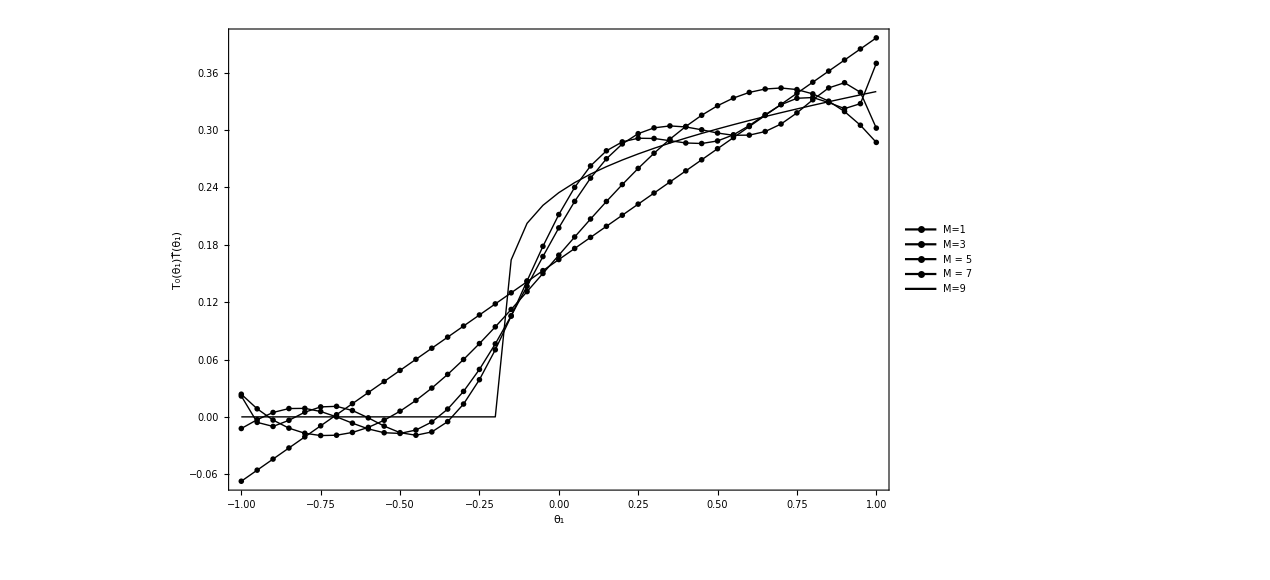
```mathematica
plotwaveexpansion =-Graphics-
```

-Graphics-

```mathematica
dataIntegrand2=Transpose@Table[{expansionfunc1dH[DriveHeCC[[200]],2,x ],expansionfunc1dH[DriveHeCC[[200]],3,x ],expansionfunc1dH[DriveHeCC[[200]],4,x ],expansionfunc1dH[DriveHeCC[[200]],5,x ] ,Tsol2[ ξfunc[AAfunc[DrivePars,x , 0, 0, 0], xlistpython[[200]],tval]](T0val+T0val/10 x)},{x,Subdivide[-1,1,50]}];
```

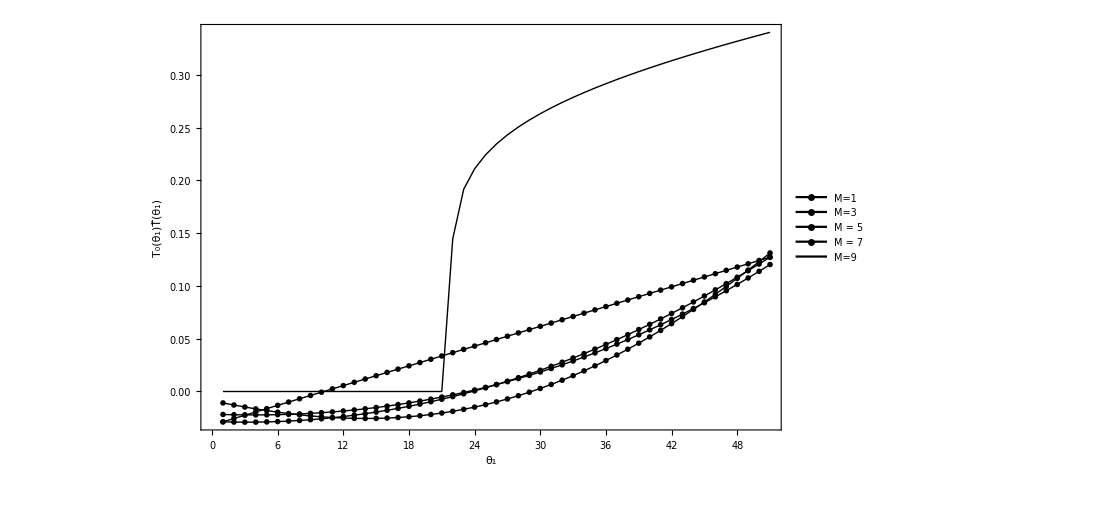

```mathematica
plotwaveexpansionH = ListPlot[dataIntegrand2,Frame->{True, True, False, False},FrameLabel->{Style["θ_1", Large],Style["T_0(θ_1)T̃(θ_1)", Large]},PlotStyle->styles6, PlotLegends->{"M=1", "M=3", "M = 5", "M = 7", "M=9"}, Joined->True, PlotMarkers->{"OpenMarkers","OpenMarkers", "OpenMarkers","OpenMarkers",None}]
```

```mathematica
Export["polynomial_expansion_plot.pdf", plotwaveexpansion];
```

```mathematica
xlistpython[[200]]
```

0.253778

```mathematica
(*AllPnCC[[;;,1,1,1,1]][[300]]*)
```

Part::partw: Part 300 of {6.4,6.38637,6.37255,6.35852,6.34429,6.32985,6.31519,6.30031,6.28519,6.26983,«90»} does not exist.

```mathematica
DrivePnExp = Table[{xlistpython[[nj]],DrivePnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
AllPnExp = Table[{xlistpython[[nj]],AllPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
TargetPnExp = Table[{xlistpython[[nj]],TargetPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
DriveHeExp = Table[{xlistpython[[nj]],DriveHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
TargetHeExp = Table[{xlistpython[[nj]],TargetHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
Length[DrivePnCC[[1]]];
(*AllPnVar = Table[{xlistpython[[nj]],1/16 Total[Table[(2/(2 i + 1))^4AllPnCC[[nj,i,i,i,i]]^2,{i,2,5}]]},{nj,1,Length[xlistpython]}];*)
DrivePnVar = Table[{xlistpython[[nj]],Total[Table[(1/(2 i + 1))DrivePnCC[[nj,i,1,1,1]]^2,{i,2,Length[DrivePnCC[[1]]]}] ]},{nj,1,Nevalpointspython}] ;
DrivePnp1std = Table[{xlistpython[[nj]],DrivePnExp[[nj]][[2]] + Sqrt[DrivePnVar[[nj]][[2]]] }, {nj,1,Nevalpointspython}];
DrivePnm1std = Table[{xlistpython[[nj]],DrivePnExp[[nj]][[2]] - Sqrt[DrivePnVar[[nj]][[2]]] }, {nj,1,Nevalpointspython}];
(*TargetPnExp = Table[{xlistpython[[nj]],1/8 TargetPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
AllPnExp = Table[{xlistpython[[nj]],1/16 AllPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
DriveHeExp = Table[{xlistpythonh[[nj]],DriveHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpythonh]}];
TargetHeExp = Table[{xlistpythonh[[nj]],TargetHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpythonh]}];
AllHeExp = Table[{xlistpythonh[[nj]],AllHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpythonh]}];*)
```

{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.,a2→0,a3→0.01134,a4→0,ω→1.2097}

```mathematica
(*Calculate analytic benchmarks for the temperature profile*)
DrivePnExpBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticDriveProfile[xlistpython[[ix]],tval, DrivePars,1]]},{ix, 1, Nevalpointspython}]; 
DrivePnVarBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticDriveProfile[xlistpython[[ix]],tval, DrivePars, 2]]- DrivePnExpBench[[ix]][[2]]^2},{ix, 1, Nevalpointspython}]; 
DrivePnstdpBench=  ParallelTable[{xlistpython[[ix]],DrivePnExpBench[[ix]][[2]]+Sqrt[DrivePnVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
DrivePnstdmBench=  ParallelTable[{xlistpython[[ix]],DrivePnExpBench[[ix]][[2]]-Sqrt[DrivePnVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
(*Hermite*)
DriveHeExpBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticDriveProfileHe[xlistpython[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpointspython}];
```

```mathematica
DriveHeVarBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticDriveProfileHe[xlistpython[[ix]],tval, DrivePars, 2]]- DriveHeExpBench[[ix]][[2]]^2},{ix, 1, Nevalpointspython}]; 
DriveHestdpBench=  ParallelTable[{xlistpython[[ix]],DriveHeExpBench[[ix]][[2]]+Sqrt[DriveHeVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
DriveHestdmBench=  ParallelTable[{xlistpython[[ix]],DriveHeExpBench[[ix]][[2]]-Sqrt[DriveHeVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}];
```

```mathematica
(*drive target errors*)
TargetPnExpBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticTargetProfile[xlistpython[[ix]],tval,AllPars,1]]},{ix, 1, Nevalpointspython}]; 
TargetPnVarBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticTargetProfile[xlistpython[[ix]],tval, AllPars,2]]- TargetPnExpBench[[ix]][[2]]^2},{ix, 1, Nevalpointspython}]; 
TargetPnstdpBench=  ParallelTable[{xlistpython[[ix]],TargetPnExpBench[[ix]][[2]]+Sqrt[TargetPnVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
TargetPnstdmBench=  ParallelTable[{xlistpython[[ix]],TargetPnExpBench[[ix]][[2]]-Sqrt[TargetPnVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}];
```

```mathematica
(*All target errors*)
```

```mathematica
AllPnExpBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticAllProfile[xlistpython[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpointspython}];
```

```mathematica
AllPnVarBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticAllProfile[xlistpython[[ix]],tval, AllPars,2]]- AllPnExpBench[[ix]][[2]]^2},{ix, 1, Nevalpointspython}]; 
AllPnstdpBench=  ParallelTable[{xlistpython[[ix]],AllPnExpBench[[ix]][[2]]+Sqrt[AllPnVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
AllPnstdmBench=  ParallelTable[{xlistpython[[ix]],AllPnExpBench[[ix]][[2]]-Sqrt[AllPnVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}];
```

```mathematica
TargetHeExpBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticTargetProfileHe[xlistpython[[ix]],tval,AllPars,1]]},{ix, 1, Nevalpointspython}];
```

```mathematica
TargetHeExpBench
```

{{0.,0.4},{0.00127527,0.39972},{0.00255054,0.39944},{0.0038258,0.399157},{0.00510107,0.398874},{0.00637634,0.398589},{0.00765161,0.398303},{0.00892688,0.398015},{0.0102021,0.397726},{0.0114774,0.397436},{0.0127527,0.397144},{0.0140279,0.396851},{0.0153032,0.396556},{0.0165785,0.39626},{0.0178538,0.395963},{0.019129,0.395664},{0.0204043,0.395363},{0.0216796,0.395061},{0.0229548,0.394758},{0.0242301,0.394453},{0.0255054,0.394146},{0.0267806,0.393838},{0.0280559,0.393529},{0.0293312,0.393217},{0.0306064,0.392905},{0.0318817,0.39259},{0.033157,0.392274},{0.0344322,0.391956},{0.0357075,0.391637},{0.0369828,0.391316},{0.038258,0.390993},{0.0395333,0.390668},{0.0408086,0.390342},{0.0420838,0.390014},{0.0433591,0.389684},{0.0446344,0.389352},{0.0459096,0.389019},{0.0471849,0.388683},{0.0484602,0.388346},{0.0497355,0.388007},{0.0510107,0.387666},{0.052286,0.387323},{0.0535613,0.386978},{0.0548365,0.386631},{0.0561118,0.386282},{0.0573871,0.385931},{0.0586623,0.385578},{0.0599376,0.385223},{0.0612129,0.384865},{0.0624881,0.384506},{0.0637634,0.384144},{0.0650387,0.383781},{0.0663139,0.383415},{0.0675892,0.383046},{0.0688645,0.382676},{0.0701397,0.382303},{0.071415,0.381928},{0.0726903,0.381551},{0.0739655,0.381171},{0.0752408,0.380788},{0.0765161,0.380404},{0.0777913,0.380016},{0.0790666,0.379627},{0.0803419,0.379234},{0.0816172,0.378839},{0.0828924,0.378442},{0.0841677,0.378042},{0.085443,0.377639},{0.0867182,0.377233},{0.0879935,0.376825},{0.0892688,0.376413},{0.090544,0.375999},{0.0918193,0.375582},{0.0930946,0.375162},{0.0943698,0.374739},{0.0956451,0.374313},{0.0969204,0.373884},{0.0981956,0.373452},{0.0994709,0.373016},{0.100746,0.372577},{0.102021,0.372135},{0.103297,0.37169},{0.104572,0.371241},{0.105847,0.370789},{0.107123,0.370333},{0.108398,0.369874},{0.109673,0.369411},{0.110948,0.368945},{0.112224,0.368474},{0.113499,0.368},{0.114774,0.367522},{0.116049,0.36704},{0.117325,0.366554},{0.1186,0.366063},{0.119875,0.365569},{0.12115,0.36507},{0.122426,0.364567},{0.123701,0.36406},{0.124976,0.363548},{0.126252,0.363031},{0.127527,0.36251},{0.128802,0.361984},{0.130077,0.361453},{0.131353,0.360917},{0.132628,0.360376},{0.133903,0.35983},{0.135178,0.359278},{0.136454,0.358721},{0.137729,0.358159},{0.139004,0.35759},{0.140279,0.357016},{0.141555,0.356436},{0.14283,0.35585},{0.144105,0.355257},{0.145381,0.354659},{0.146656,0.354053},{0.147931,0.353441},{0.149206,0.352822},{0.150482,0.352196},{0.151757,0.351562},{0.153032,0.350921},{0.154307,0.350272},{0.155583,0.349616},{0.156858,0.348951},{0.158133,0.348277},{0.159409,0.347595},{0.160684,0.346904},{0.161959,0.346204},{0.163234,0.345494},{0.16451,0.344773},{0.165785,0.344042},{0.16706,0.343301},{0.168335,0.342548},{0.169611,0.341782},{0.170886,0.341005},{0.172161,0.340214},{0.173436,0.339408},{0.174712,0.338588},{0.175987,0.337753},{0.177262,0.3369},{0.178538,0.336029},{0.179813,0.335139},{0.181088,0.334229},{0.182363,0.333291},{0.183639,0.332336},{0.184914,0.331352},{0.186189,0.33034},{0.187464,0.329292},{0.18874,0.328219},{0.190015,0.327102},{0.19129,0.325955},{0.192565,0.324764},{0.193841,0.323529},{0.195116,0.322249},{0.196391,0.320913},{0.197667,0.319526},{0.198942,0.31806},{0.200217,0.316548},{0.201492,0.314945},{0.202768,0.313304},{0.204043,0.311548},{0.205318,0.309744},{0.206593,0.307808},{0.207869,0.305814},{0.209144,0.303706},{0.210419,0.3015},{0.211694,0.299241},{0.21297,0.296807},{0.214245,0.294304},{0.21552,0.291624},{0.216796,0.288852},{0.218071,0.286032},{0.219346,0.283144},{0.220621,0.280143},{0.221897,0.276805},{0.223172,0.27348},{0.224447,0.270088},{0.225722,0.266564},{0.226998,0.262664},{0.228273,0.25897},{0.229548,0.255168},{0.230824,0.251174},{0.232099,0.247269},{0.233374,0.242934},{0.234649,0.238785},{0.235925,0.234414},{0.2372,0.230049},{0.238475,0.225626},{0.23975,0.220489},{0.241026,0.215902},{0.242301,0.211311},{0.243576,0.206845},{0.244851,0.20225},{0.246127,0.197137},{0.247402,0.192304},{0.248677,0.187388},{0.249953,0.181975},{0.251228,0.177822},{0.252503,0.172338},{0.253778,0.167838},{0.255054,0.162988},{0.256329,0.157834},{0.257604,0.1529},{0.258879,0.148337},{0.260155,0.143612},{0.26143,0.138937},{0.262705,0.133941},{0.26398,0.129442},{0.265256,0.123923},{0.266531,0.119811},{0.267806,0.115655},{0.269082,0.111657},{0.270357,0.107041},{0.271632,0.103195},{0.272907,0.0990429},{0.274183,0.0952236},{0.275458,0.0906779},{0.276733,0.0871522},{0.278008,0.0836502},{0.279284,0.080465},{0.280559,0.0768456},{0.281834,0.0737523},{0.28311,0.0704856},{0.284385,0.0677136},{0.28566,0.065072},{0.286935,0.0622702},{0.288211,0.0593283},{0.289486,0.0566604},{0.290761,0.0517111},{0.292036,0.0490327},{0.293312,0.0468859},{0.294587,0.0448734},{0.295862,0.0428596},{0.297137,0.0409469},{0.298413,0.0391518},{0.299688,0.0367631},{0.300963,0.0351484},{0.302239,0.0316535},{0.303514,0.0300071},{0.304789,0.0275503},{0.306064,0.0265053},{0.30734,0.0253503},{0.308615,0.0241757},{0.30989,0.0226858},{0.311165,0.0216245},{0.312441,0.0206213},{0.313716,0.0195767},{0.314991,0.0184002},{0.316266,0.0172933},{0.317542,0.0164491},{0.318817,0.0157565},{0.320092,0.0147285},{0.321368,0.0139602},{0.322643,0.0132772},{0.323918,0.0124576},{0.325193,0.0118226},{0.326469,0.011222},{0.327744,0.0106306},{0.329019,0.0100412},{0.330294,0.00949268},{0.33157,0.00895667},{0.332845,0.00845094},{0.33412,0.00693903},{0.335395,0.00660951},{0.336671,0.00624426},{0.337946,0.00588877},{0.339221,0.00556338},{0.340497,0.00534293},{0.341772,0.00511876},{0.343047,0.00482716},{0.344322,0.00410666},{0.345598,0.00388152},{0.346873,0.00350558},{0.348148,0.00321209},{0.349423,0.00292847},{0.350699,0.0027613},{0.351974,0.00260797},{0.353249,0.0024616},{0.354525,0.00232478},{0.3558,0.00219198},{0.357075,0.00207333},{0.35835,0.00193953},{0.359626,0.00183928},{0.360901,0.0017348},{0.362176,0.00162584},{0.363451,0.00153218},{0.364727,0.00141983},{0.366002,0.00133572},{0.367277,0.00125768},{0.368552,0.000777723},{0.369828,0.000731553},{0.371103,0.000664522},{0.372378,0.00062729},{0.373654,0.000592116},{0.374929,0.000558606},{0.376204,0.000526882},{0.377479,0.000495816},{0.378755,0.000409908},{0.38003,0.000386606},{0.381305,0.000364205}}

```mathematica
TargetHeVarBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticTargetProfileHe[xlistpython[[ix]],tval, AllPars,2]]- TargetHeExpBench[[ix]][[2]]^2},{ix, 1, Nevalpointspython}];
```

```mathematica
TargetHestdpBench=  ParallelTable[{xlistpython[[ix]],TargetHeExpBench[[ix]][[2]]+Sqrt[TargetHeVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
TargetHestdmBench=  ParallelTable[{xlistpython[[ix]],TargetHeExpBench[[ix]][[2]]-Sqrt[TargetHeVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}];
```

```mathematica
|
```

```mathematica
AllHeExpBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticAllProfileHe[xlistpython[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpointspython}];
```

```mathematica
AllHeVarBench=  ParallelTable[{xlistpython[[ix]],Quiet[analyticAllProfileHe[xlistpython[[ix]],tval, AllPars,2]]- AllHeExpBench[[ix]][[2]]^2},{ix, 1, Nevalpointspython}]; 
AllHestdpBench=  ParallelTable[{xlistpython[[ix]],AllHeExpBench[[ix]][[2]]+Sqrt[AllHeVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}]; 
AllHestdmBench=  ParallelTable[{xlistpython[[ix]],AllHeExpBench[[ix]][[2]]-Sqrt[AllHeVarBench[[ix]][[2]]]},{ix, 1, Nevalpointspython}];
```

```mathematica
Print[RMSE[AllPnExpBench[[;;,2]], AllPnExp[[;;,2]]], "RMSE EXP ALL PN"]
Print[RMSE[DrivePnExpBench[[;;,2]],DrivePnExp[[;;,2]]], "RMSE EXP DRIVE PN"]
Print[RMSE[TargetPnExpBench[[;;,2]], TargetPnExp[[;;,2]]], "RMSE EXP TARGET PN"]
```

0.000365904RMSE EXP ALL PN

0.000469133RMSE EXP DRIVE PN

0.00167576RMSE EXP TARGET PN

```mathematica
(*ListPlot[{AllPnVar,DrivePnVar},Joined->True, PlotRange->All]
ListPlot[{stdplusdrivepn},Joined->True, PlotRange->All]*)
(*ListPlot[{DrivePnVar,DrivePnVarBench}, Joined->True]*)
```

```mathematica
(*ListPlot[{DrivePnExp,DrivePnp1std, DrivePnm1std , DrivePnExpBench},Joined->True, PlotLegends->{"pn drive", "pn target", "pn all", "Pn bench"}]
ListPlot[{(*DriveHeExp ,TargetHeExp,*)AllHeExp},Joined->True, PlotLegends->{ "he drive", "he target", "he all"}, PlotRange->All]*)
```

```mathematica
(*Load samples*)
allPnsamples = Import["all_Pn_samples.hdf5",{"Datasets","samples"}];
drivePnsamples = Import["drive_Pn_samples.hdf5",{"Datasets","samples"}];
targetPnsamples = Import["target_Pn_samples.hdf5",{"Datasets","samples"}];
drivePnMC= Import["mc_samples_pn.hdf5",{"Datasets","drive"}];
targetPnMC= Import["mc_samples_pn.hdf5",{"Datasets","target"}];
allPnMC= Import["mc_samples_pn.hdf5",{"Datasets","all"}];
(*medianallpn = Table[0,{j,1, Nevalpointspython}];
twentiethallpn = Table[0,{j,1, Nevalpointspython}];
eightiethallpn= Table[0,{j,1, Nevalpointspython}];*)
driveHesamples = Import["drive_He_samples.hdf5",{"Datasets","samples"}];
targetHesamples = Import["target_He_samples.hdf5",{"Datasets","samples"}];
allHesamples = Import["all_He_samples.hdf5",{"Datasets","samples"}];
driveHeMC= Import["mc_samples_he.hdf5",{"Datasets","drive"}];
targetHeMC= Import["mc_samples_he.hdf5",{"Datasets","target"}];
allHeMC= Import["mc_samples_he.hdf5",{"Datasets","all"}];
mediandrivepn =plottable[drivePnsamples[[1]]];
twentiethdrivepn= plottable[drivePnsamples[[2]]];
eightiethdrivepn= plottable[drivePnsamples[[3]]];

mediantargetpn =plottable[targetPnsamples[[1]]];
twentiethtargetpn= plottable[targetPnsamples[[2]]];
eightiethtargetpn= plottable[targetPnsamples[[3]]];

medianallpn =plottable[allPnsamples[[1]]];
twentiethallpn= plottable[allPnsamples[[2]]];
eightiethallpn= plottable[allPnsamples[[3]]];

mediandrivepnMC = plottable[drivePnMC[[1]]];
twentiethdrivepnMC= plottable[drivePnMC[[2]]];
eightiethdrivepnMC= plottable[drivePnMC[[3]]];

mediantargetpnMC = plottable[targetPnMC[[1]]];
twentiethtargetpnMC= plottable[targetPnMC[[2]]];
eightiethtargetpnMC= plottable[targetPnMC[[3]]];

medianallpnMC = plottable[allPnMC[[1]]];
twentiethallpnMC= plottable[allPnMC[[2]]];
eightiethallpnMC= plottable[allPnMC[[3]]];

mediandrivehe =plottable[driveHesamples[[1]]];
twentiethdrivehe= plottable[driveHesamples[[2]]];
eightiethdrivehe= plottable[driveHesamples[[3]]];
meandrivehe = plottable[driveHesamples[[4]]];

mediantargethe=plottable[targetHesamples[[1]]];
twentiethtargethe= plottable[targetHesamples[[2]]];
eightiethtargethe= plottable[targetHesamples[[3]]];

mediandriveheMC = plottable[driveHeMC[[1]]];
twentiethdriveheMC= plottable[driveHeMC[[2]]];
eightiethdriveheMC= plottable[driveHeMC[[3]]];
meandriveheMC = plottable[driveHeMC[[4]]];

medianallheMC = plottable[allHeMC[[1]]];
twentiethallheMC= plottable[allHeMC[[2]]];
eightiethallheMC= plottable[allHeMC[[3]]];

mediantargetheMC = plottable[targetHeMC[[1]]];
twentiethtargetheMC= plottable[targetHeMC[[2]]];
eightiethtargetheMC= plottable[targetHeMC[[3]]];
```

```mathematica
Length[driveHesamples[[1]]]
plottable[list_]:= Table[{xlistpython[[nj]], list[[nj]]},{nj,1,Nevalpointspython}]
```

300

```mathematica
|
```

```mathematica
(*Plot*)
```

```mathematica
nominal = Table[{xlistpython[[nj]],Tsol2[ ξfunc[AAfunc[AllPars,0, 0, 0, 0], xlistpython[[nj]],tval]]*T0val},{nj,1,Length[xlistpython]}];
(*meansampled = Table[{xlistpython[[nj]], Mean[drivePnsamples[[nj]]]},{nj,1,Nevalpointspython}];*)
```

```mathematica
(*ListPlot[{mediandrivepn,twentiethdrivepn[[1;;300]],eightiethdrivepn, DrivePnExp, meansampled, DrivePnp1std, DrivePnm1std},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Median", "20^th percentile", "80^th percentile", "expectation", "mean sampled", "+1σ","-1σ"}]*)
styles5=Flatten@Table[{Directive[Dashed, color, Thick],Directive[Dashed,color, Thick],Directive[Dashed,color, Thick],Directive[color, Thick], Directive[color, Thick], Directive[color, Thick], Directive[DotDashed,color, Thick],  Directive[Dashed,Gray, Thick],  Directive[Dotted,color, Thick],  Directive[Dotted,color, Thick]},{color,{Black,Gray}} ]; 
PLOTDRIVEPROFILEPN = ListPlot[{mediandrivepn,twentiethdrivepn[[1;;300]],eightiethdrivepn, mediandrivepnMC[[1;;-1;;1]],twentiethdrivepnMC[[1;;300]],eightiethdrivepnMC, nominal, DrivePnExpBench, DrivePnstdpBench, DrivePnstdmBench},Joined->True,PlotMarkers->False, PlotStyle->styles5,Frame->{True, True, False, False}, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Expansion", None, None, "Monte Carlo",None,None, "nominal", "Expectation", "+1σ", "-1σ"}, PlotRange->{{0., 0.42},{-0.05, 0.45}}, Epilog->{Text[Style["median",Black,Bold,  Medium],{0.15,0.34}], Text[Style["20^th percentile",Black,Bold,  Medium],{0.15,0.3}], Text[Style["80^th percentile",Black,Bold,  Medium],{0.15,0.37}]}]
(*ListPlot[{mediantargetpn,twentiethtargetpn[[1;;90]],eightiethtargetpn , TargetPnExp, nominal},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Median", "20^th percentile", "80^th percentile", "expectation", "nominal"}]
ListPlot[{medianallpn,twentiethallpn[[1;;95]],eightiethallpn ,AllPnExp,nominal},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Median", "20^th percentile", "80^th percentile", "expectation", "nominal"}]*)
```

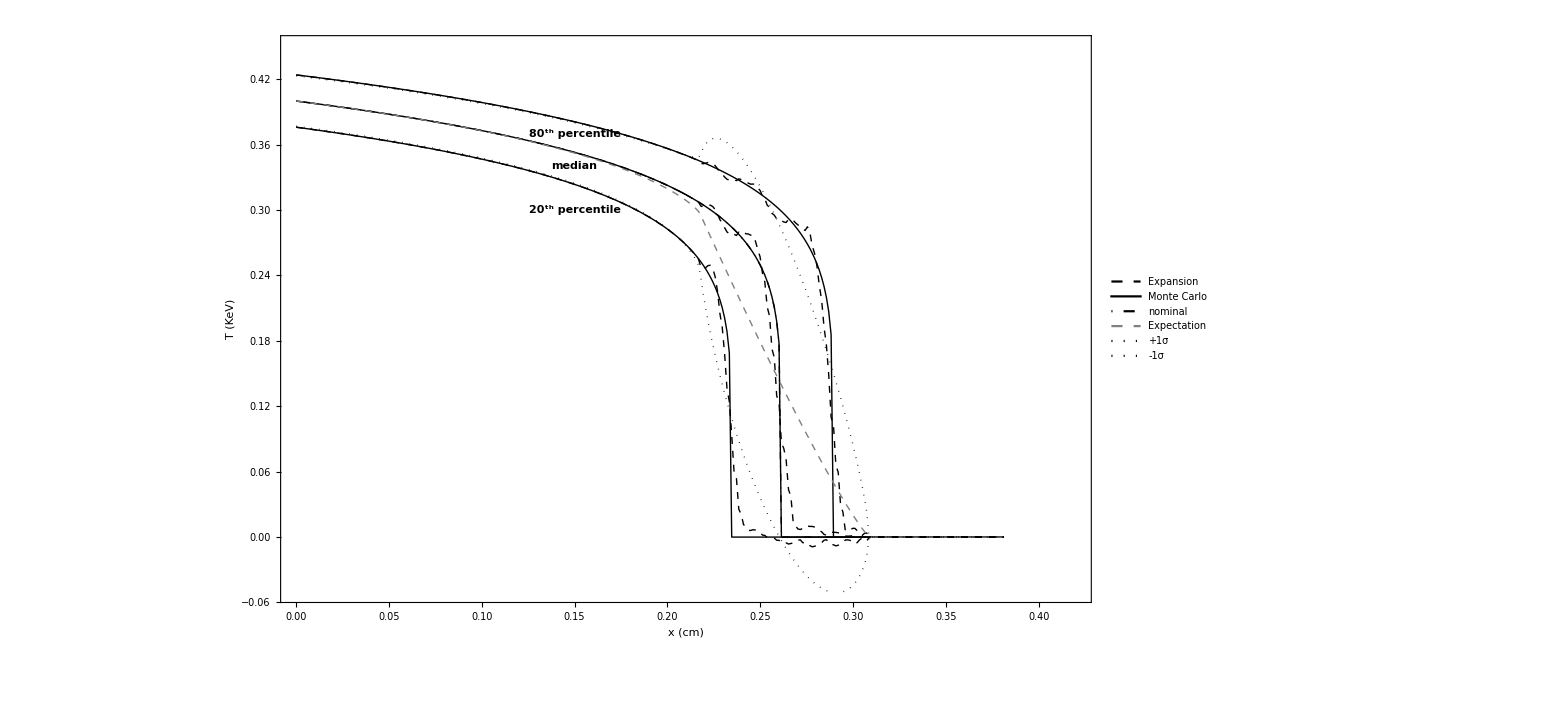
```mathematica
PLOTDRIVEPROFILEPN = -Graphics-
```

-Graphics-

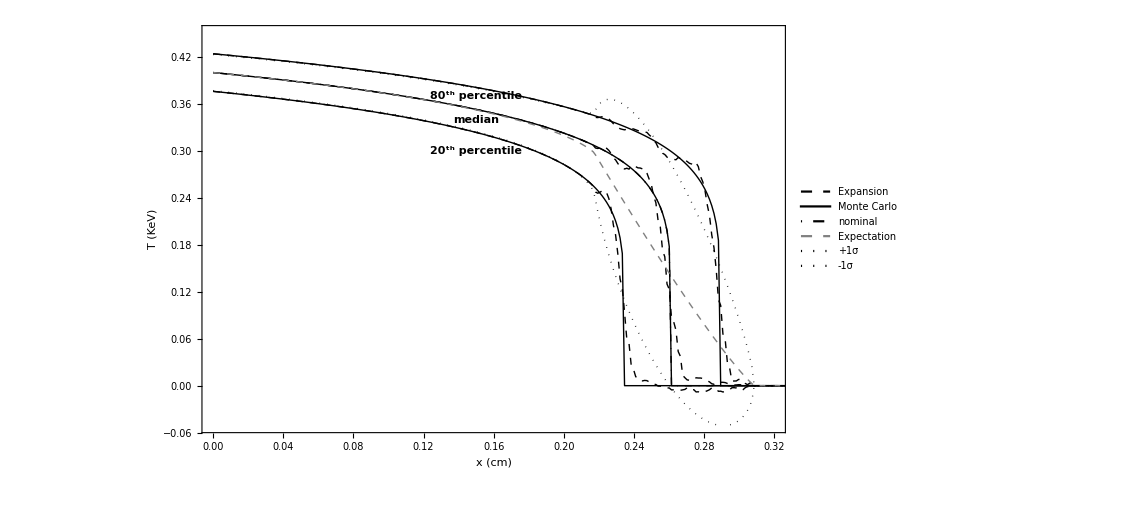

drive_pn_profile.pdf

```mathematica
PLOTTARGETPROFILEPN = ListPlot[{(*mediantargetpn,twentiethtargetpn[[1;;300]],eightiethtargetpn,*) mediantargetpnMC[[1;;-1;;1]],twentiethtargetpnMC[[1;;300]],eightiethtargetpnMC, nominal,TargetPnExpBench, TargetPnstdpBench, TargetPnstdmBench},Joined->True,PlotMarkers->False, PlotStyle->styles7,Frame->{True, True, False, False}, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{ "Monte Carlo",None,None, "nominal", "Expectation", "+1σ", "-1σ"}, PlotRange->{{0., 0.42},{-0.05, 0.45}}, Epilog->{Text[Style["median",Black,Bold,  Medium],{0.24,0.26}], Text[Style["20^th percentile",Black,Bold,  Medium],{0.2,0.28}], Text[Style["80^th percentile",Black,Bold,  Medium],{0.25,0.32}]}]
```

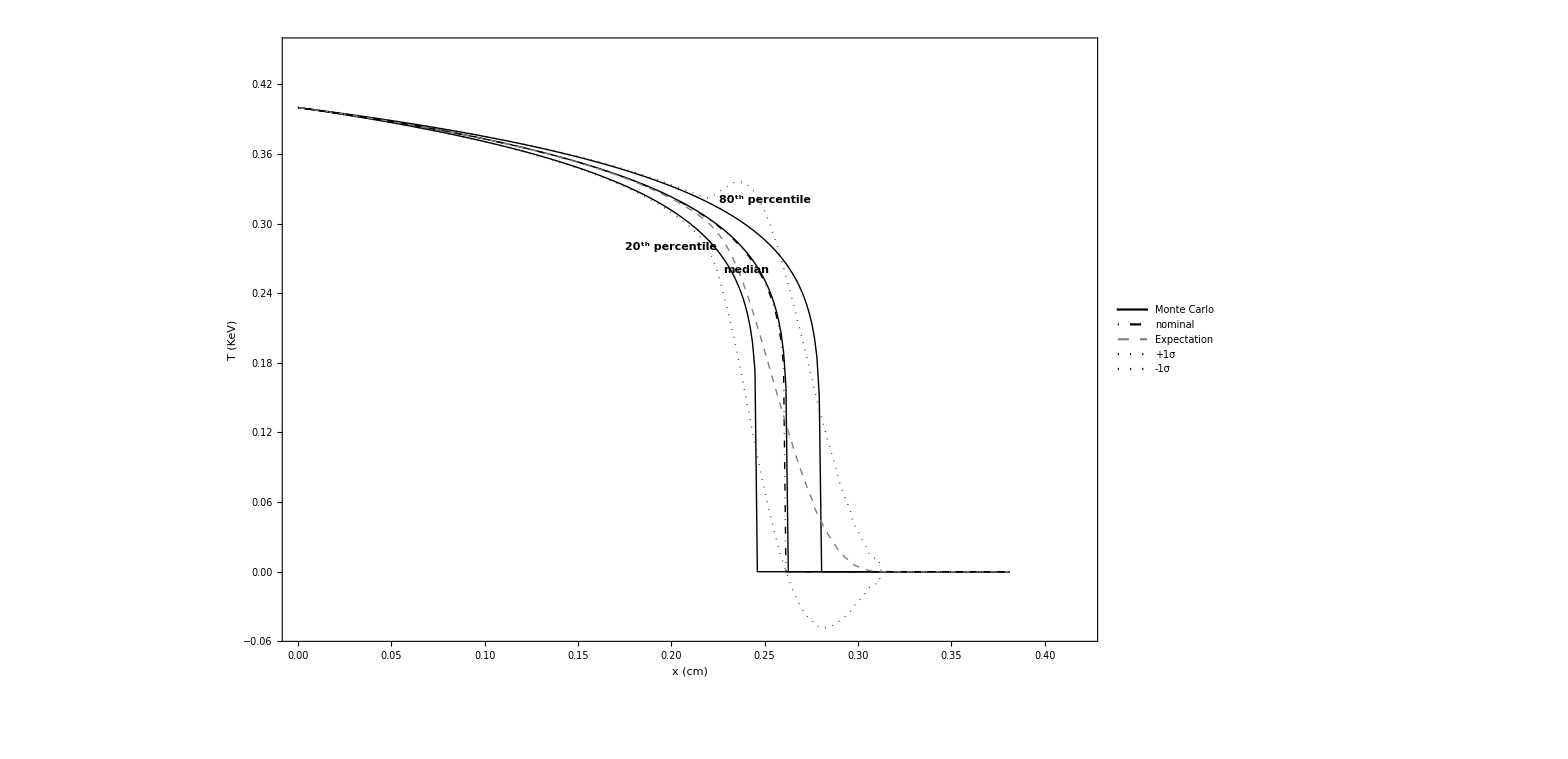
```mathematica
PLOTTARGETPROFILEPN = -Graphics-
```

-Graphics-

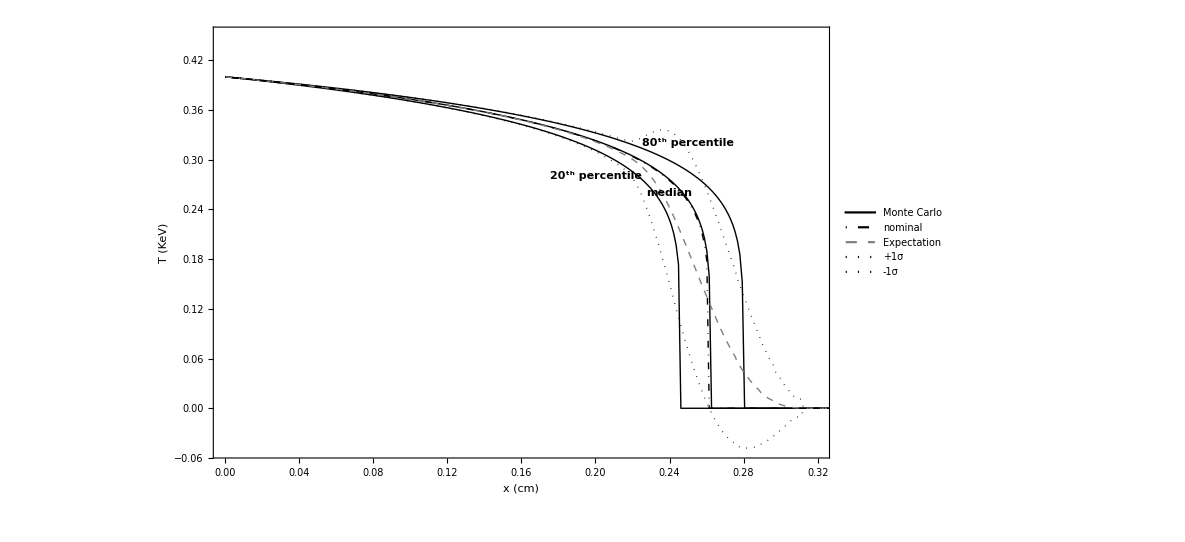
```mathematica
PLOTTARGETPROFILEPN = -Graphics-
```

-Graphics-

target_pn_profile.pdf

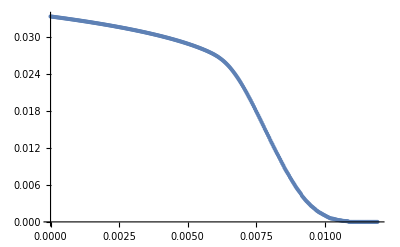

```mathematica
(*  AllPnExpBench[[;;,2]]=AllPnExpBench[[;;,2]]*6/16;*)
```

```mathematica
(* AllPnExpBench*)
```

```mathematica
styles7=Flatten@Table[{Directive[color, Thick], Directive[color, Thick], Directive[color, Thick], Directive[DotDashed,color, Thick, Bold],  Directive[Dashed,Gray, Thick, Bold],  Directive[Dotted,color, Thick, Bold],  Directive[Dotted,color, Thick, Bold]},{color,{Black,Gray}} ];
```

```mathematica
PLOTALLPROFILEPN = ListPlot[{(*medianallpn,twentiethallpn[[1;;300]],eightiethallpn,*) medianallpnMC[[1;;-1;;1]],twentiethallpnMC[[1;;300]],eightiethallpnMC, nominal, AllPnExpBench, AllPnstdpBench, AllPnstdmBench},Joined->True,PlotMarkers->False, PlotStyle->styles7,Frame->{True, True, False, False}, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{  "Monte Carlo",None,None, "nominal", "Expectation", "+1σ", "-1σ"}, PlotRange->{{0., 0.42},{-0.05, 0.45}}, Epilog->{Text[Style["median",Black,Bold,  Medium],{0.15,0.34}], Text[Style["20^th percentile",Black,Bold,  Medium],{0.15,0.3}], Text[Style["80^th percentile",Black,Bold,  Medium],{0.15,0.37}]}]
```

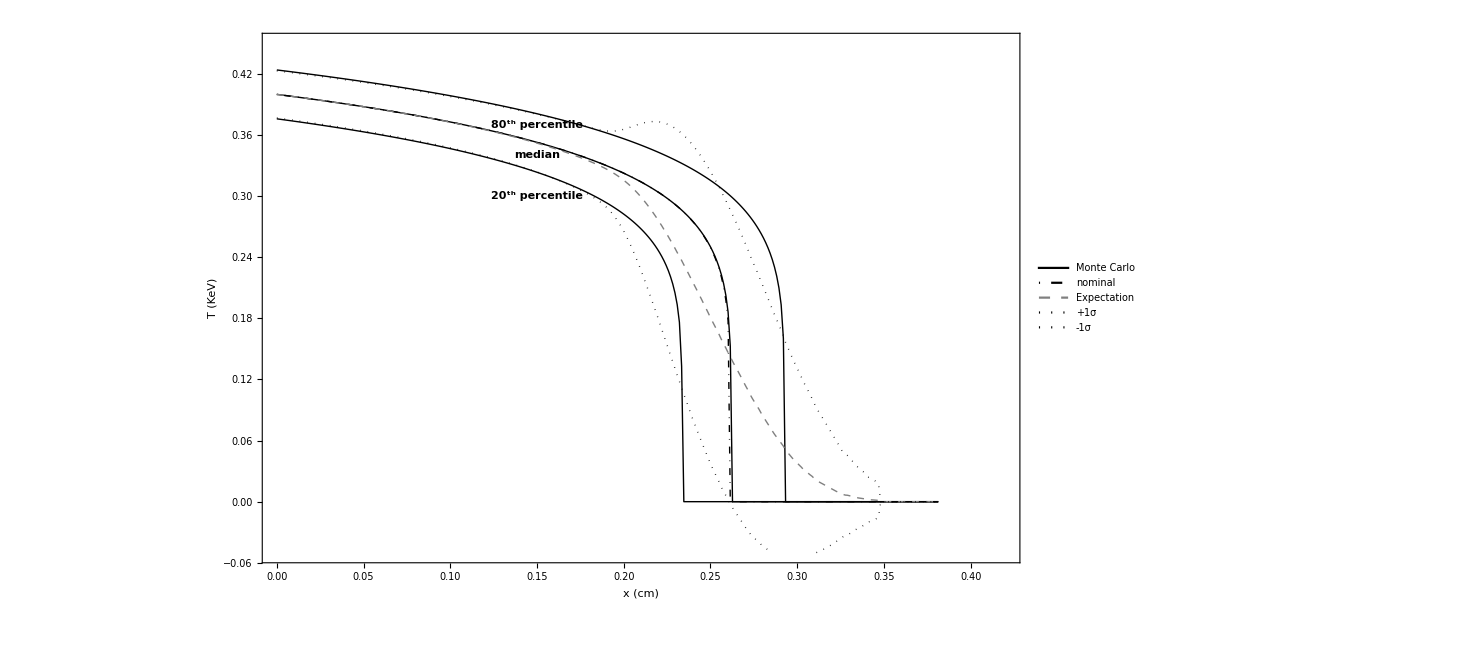
```mathematica
PLOTALLPROFILEPN = -Graphics-
```

-Graphics-

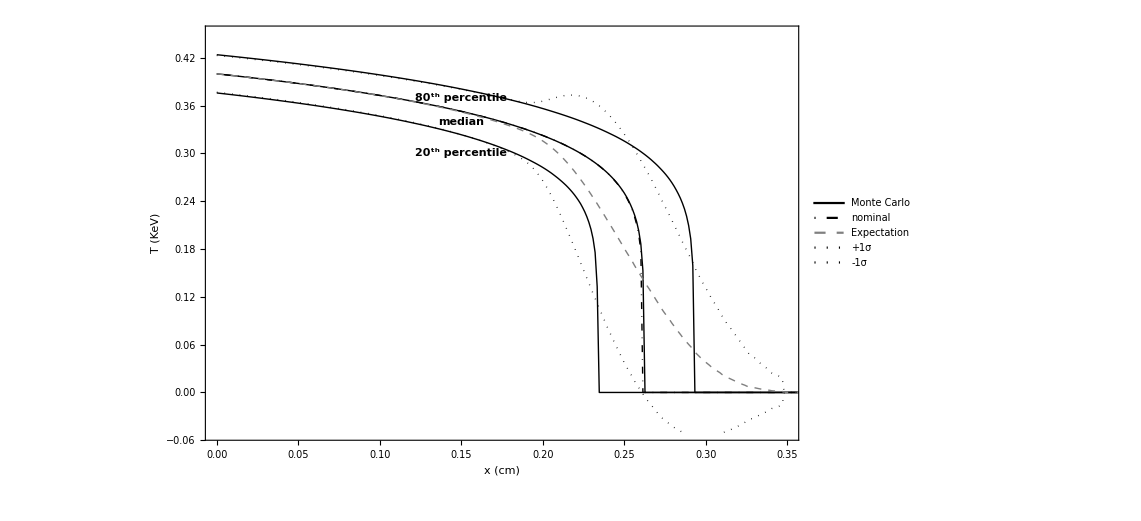
```mathematica
PLOTALLPROFILEPN = -Graphics-
```

-Graphics-

all_profle_pn.pdf

```mathematica
AllPnstdmBench
```

{{0.,0.40000011260847-√(-1.137778418395+analyticAllrofile[0.,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},2])},298,{0.381305,-√analyticAllrofile[0.381305,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},2]}}
 |  |  |  |

```mathematica
(*ListPlot[{medianallpn,twentiethallpn[[1;;95]], eightiethallpn, AllPnExp}, Joined->True, PlotLegends->{"Median", "20^th percentile", "80^th percentile", "Mean"}]*)

(*ListPlot[{mediandrivepn,twentiethdrivepn[[1;;80]],eightiethdrivepn}, Joined->True, PlotLegends->{"Median", "20^th percentile", "80^th percentile", "Mean"}, ]*)
```

```mathematica
PLOTDRIVEPROFILEHe = ListPlot[{(*mediandrivehe,twentiethdrivehe[[1;;300]],eightiethdrivehe,*) mediandriveheMC[[1;;-1;;1]],twentiethdriveheMC[[1;;300]],eightiethdriveheMC, nominal, DriveHeExpBench, DriveHestdpBench, DriveHestdmBench},Joined->True,PlotMarkers->False, PlotStyle->styles7,Frame->{True, True, False, False}, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{(*"Expansion", None, None,*) "Monte Carlo",None,None, "nominal", "Expectation", "+1σ", "-1σ"}, PlotRange->{{0., .42},{-0.05, 0.45}}, Epilog->{Text[Style["median",Black,Bold,  Medium],{0.15,0.34}], Text[Style["20^th percentile",Black,Bold,  Medium],{0.15,0.3}], Text[Style["80^th percentile",Black,Bold,  Medium],{0.15,0.37}]}]
```

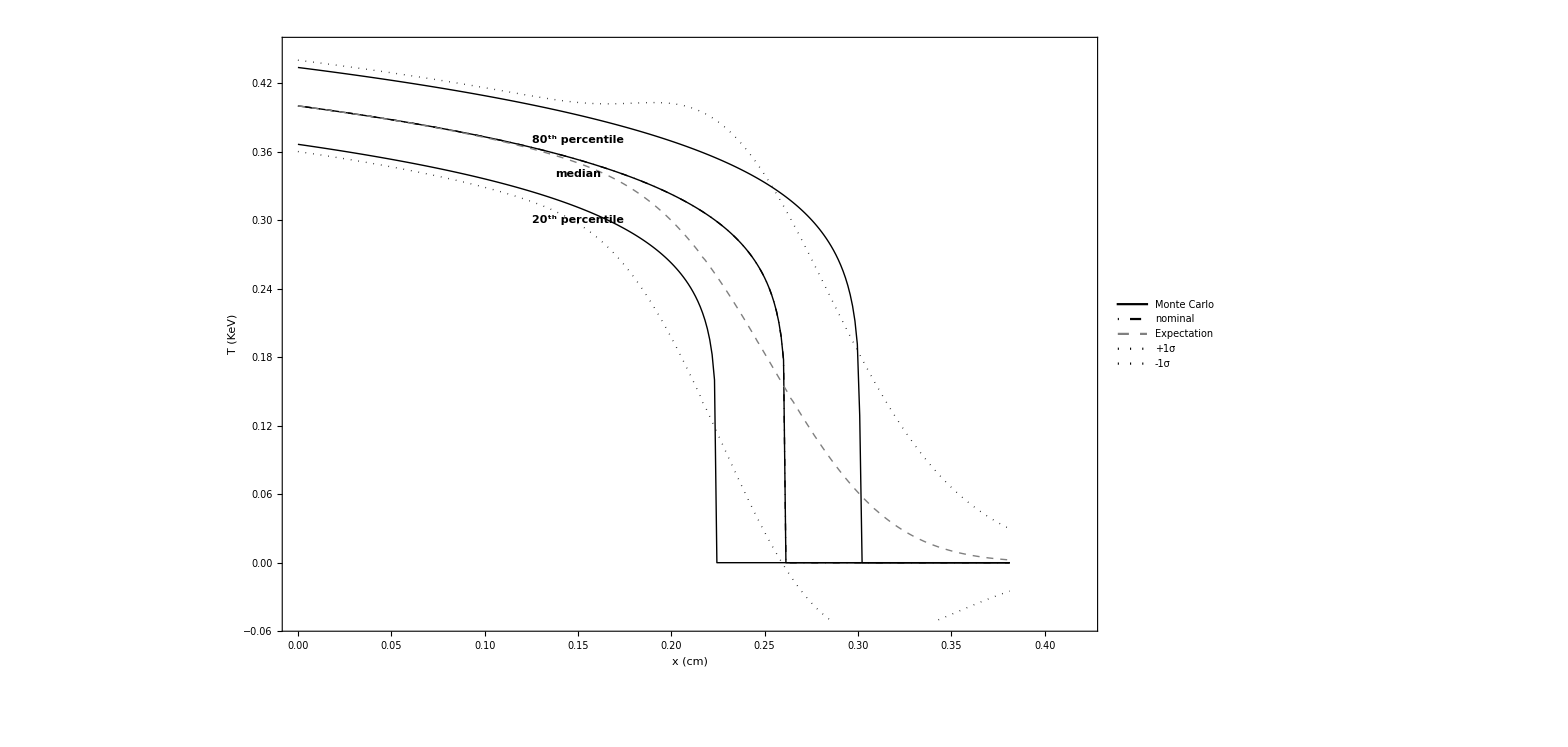
```mathematica
PLOTDRIVEPROFILEHe = -Graphics-
```

-Graphics-

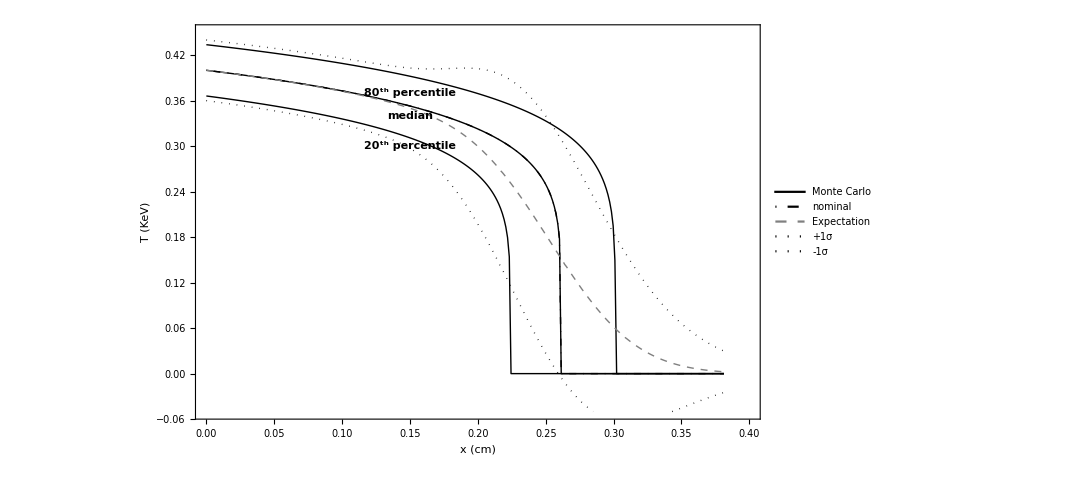
```mathematica
PLOTDRIVEPROFILEHe = -Graphics-
```

-Graphics-

drive_profile_he.pdf

```mathematica
PLOTTARGETPROFILEHe = ListPlot[{(*mediandrivehe,twentiethdrivehe[[1;;300]],eightiethdrivehe,*) mediantargetheMC[[1;;-1;;1]],twentiethtargetheMC[[1;;300]],eightiethtargetheMC, nominal, TargetHeExpBench,TargetHestdpBench, TargetHestdmBench},Joined->True,PlotMarkers->False, PlotStyle->styles7,Frame->{True, True, False, False}, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{(*"Expansion", None, None,*) "Monte Carlo",None,None, "nominal", "Expectation", "+1σ", "-1σ"}, PlotRange->{{0., .42},{-0.05, 0.45}}, Epilog->{Text[Style["median",Black,Bold,  Medium],{0.26,0.14}], Text[Style["20^th percentile",Black,Bold,  Medium],{0.15,0.32}], Text[Style["80^th percentile",Black,Bold,  Medium],{0.15,0.37}]}]
```

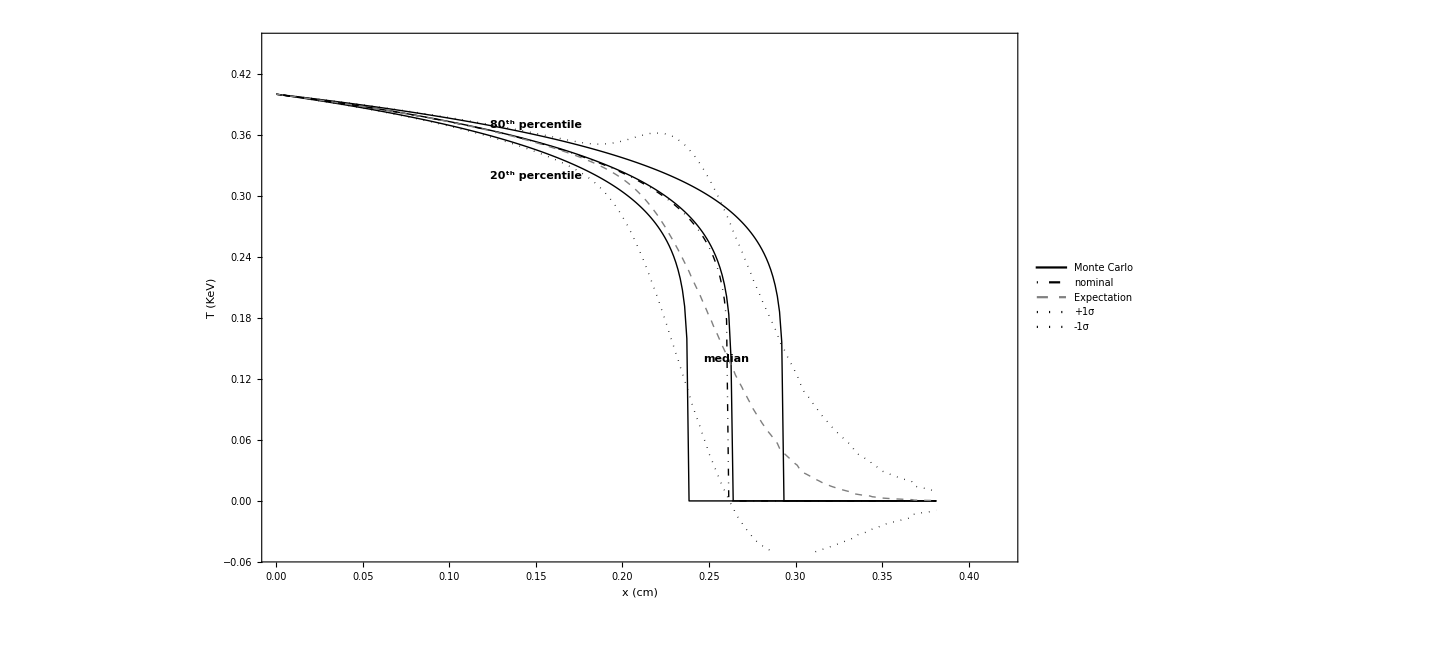
```mathematica
PLOTTARGETPROFILEHe = -Graphics-
```

-Graphics-

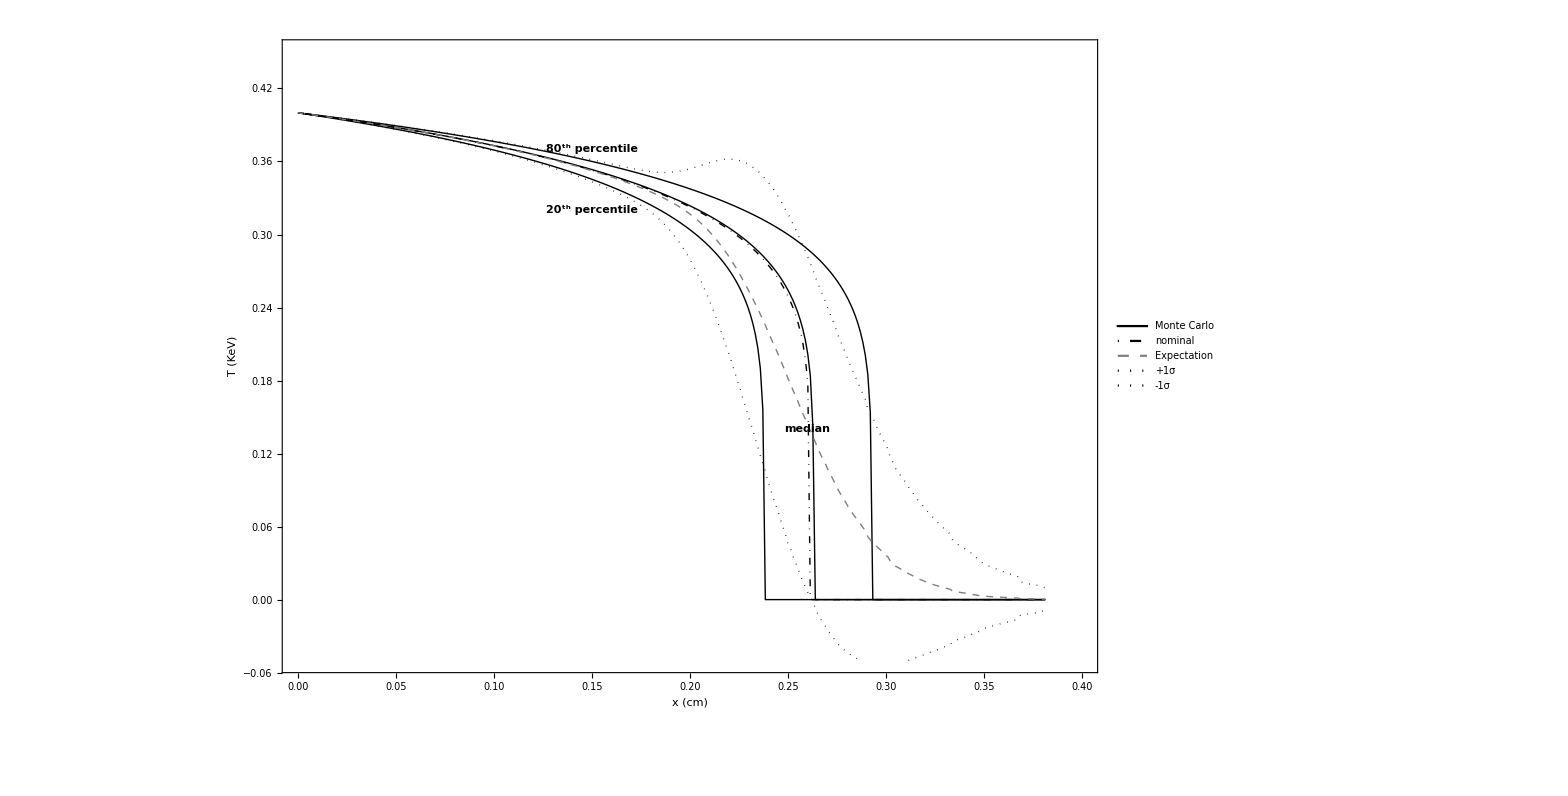
```mathematica
PLOTTARGETPROFILEHe = -Graphics-
```

-Graphics-

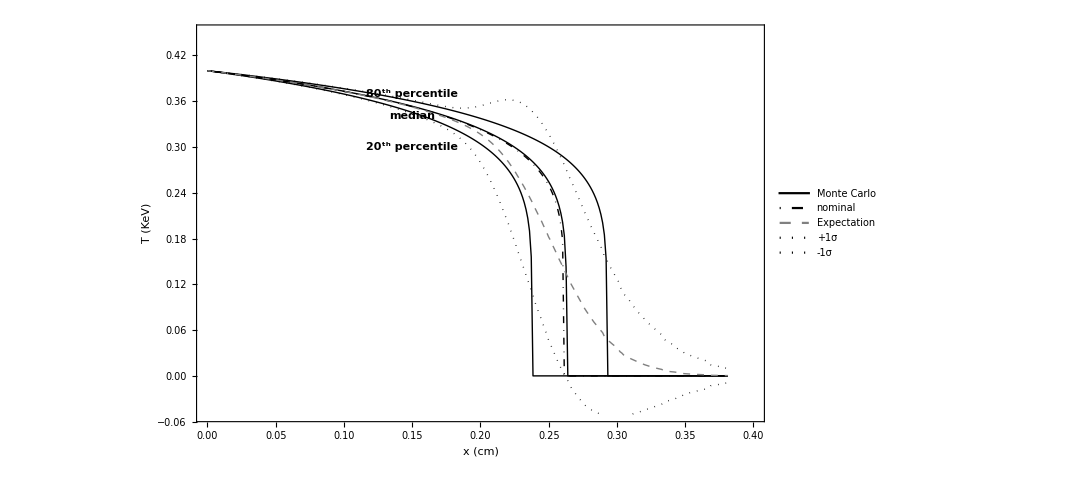
```mathematica
PLOTTARGETPROFILEHe = -Graphics-
```

-Graphics-

target_profile_he.pdf

```mathematica
t
```

teval

```mathematica
PLOTALLPROFILEHe = ListPlot[{(*mediandrivehe,twentiethdrivehe[[1;;300]],eightiethdrivehe,*) medianallheMC[[1;;-1;;1]],twentiethallheMC[[1;;300]],eightiethallheMC, nominal, AllHeExpBench,AllHestdpBench, AllHestdmBench},Joined->True,PlotMarkers->False, PlotStyle->styles7,Frame->{True, True, False, False}, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{(*"Expansion", None, None,*) "Monte Carlo",None,None, "nominal", "Expectation", "+1σ", "-1σ"}, PlotRange->{{0., .42},{-0.05, 0.45}}, Epilog->{Text[Style["median",Black,Bold,  Medium],{0.15,0.34}], Text[Style["20^th percentile",Black,Bold,  Medium],{0.15,0.3}], Text[Style["80^th percentile",Black,Bold,  Medium],{0.15,0.37}]}]
```

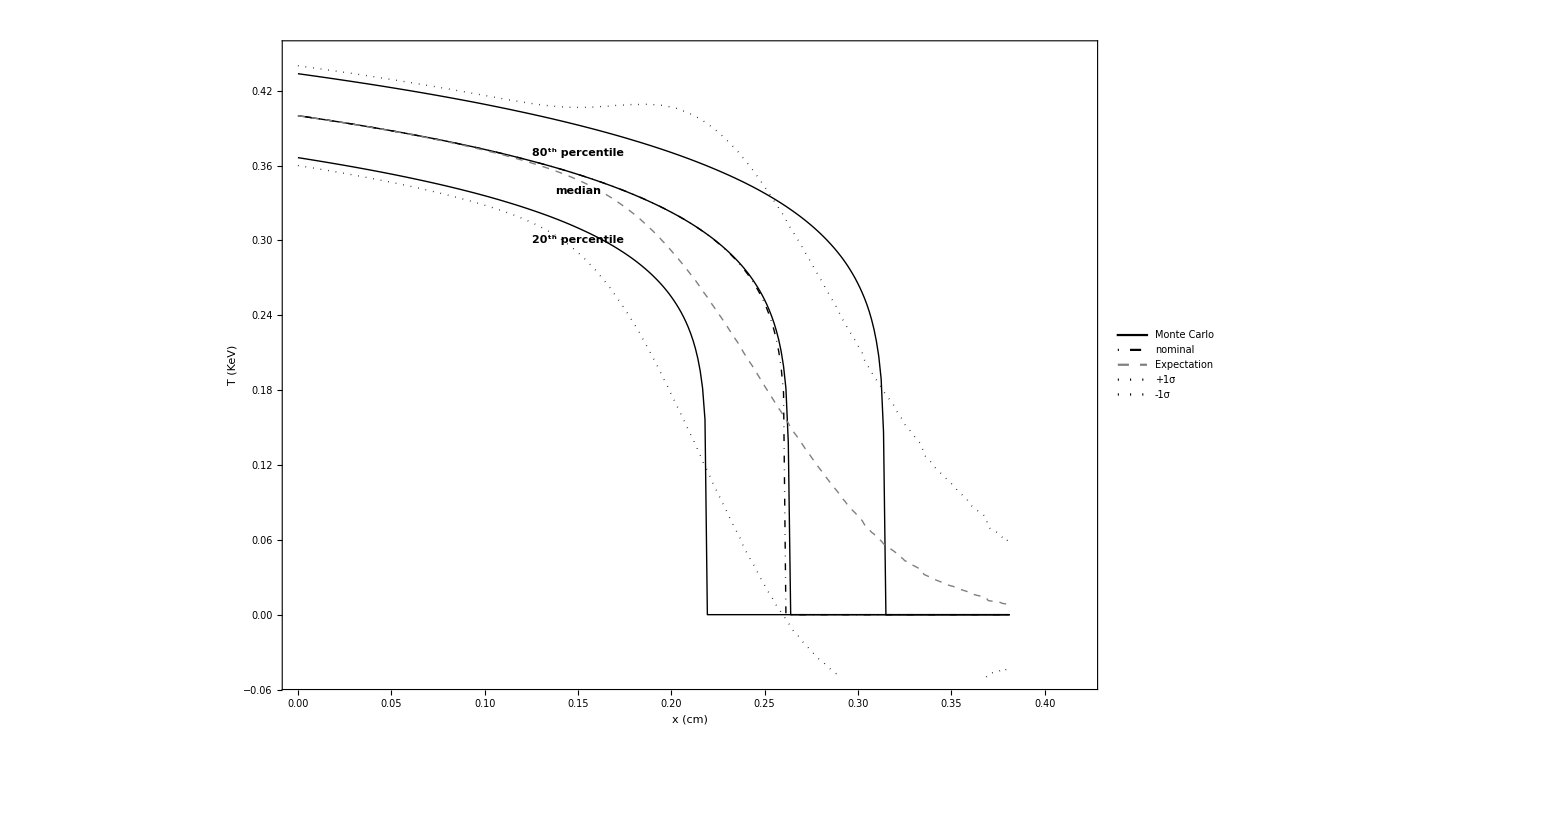
```mathematica
PLOTALLPROFILEHe = -Graphics-
```

-Graphics-

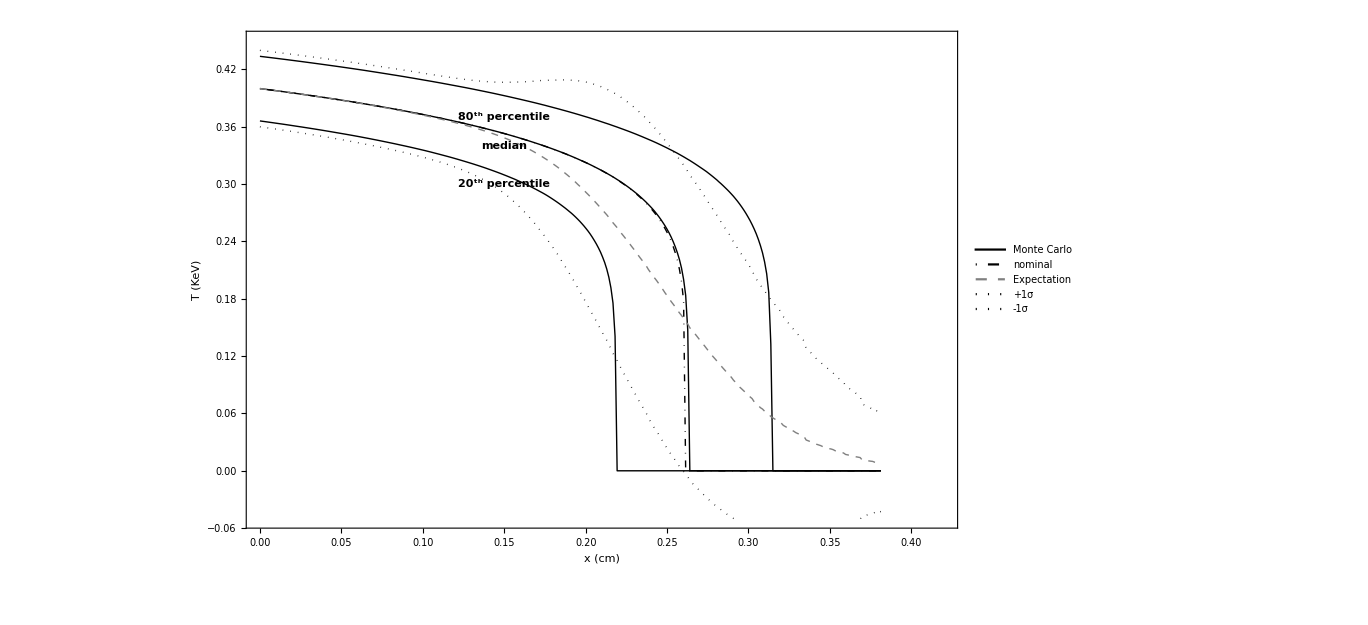
```mathematica
PLOTALLPROFILEHe = -Graphics-
```

-Graphics-

```mathematica
Export["target_profile_he.pdf",PLOTTARGETPROFILEHe];
Export["all_profile_he.pdf", PLOTALLPROFILEHe];
Export["drive_profile_he.pdf", PLOTDRIVEPROFILEHe];
Export["all_profle_pn.pdf", PLOTALLPROFILEPN];
Export["drive_pn_profile.pdf", PLOTDRIVEPROFILEPN];
Export["target_pn_profile.pdf", PLOTTARGETPROFILEPN];
```

```mathematica
RMSE[DriveHeExpBench[[;;,2]], DriveHeExp[[;;,2]]]
```

0.0616874

```mathematica
Length[DriveHeExpBench]
```

300

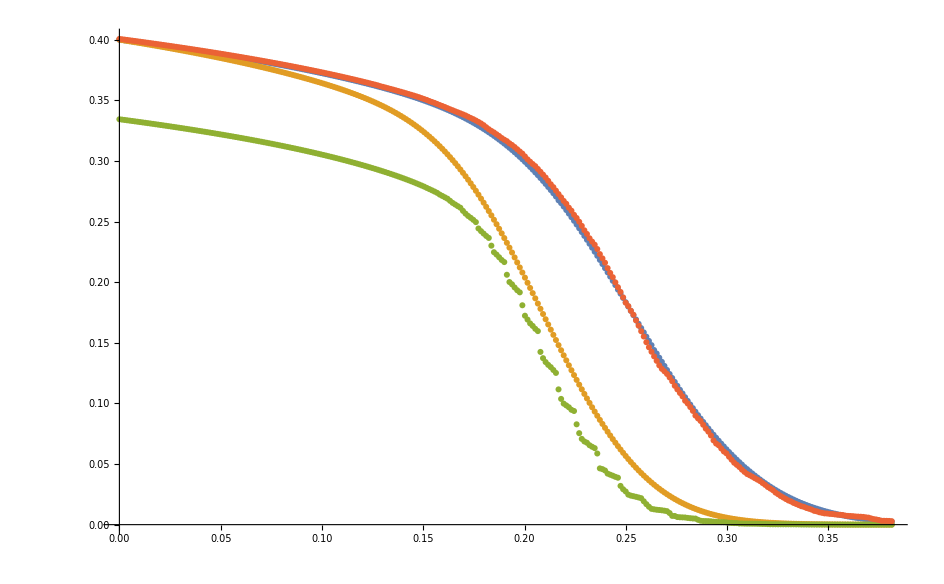

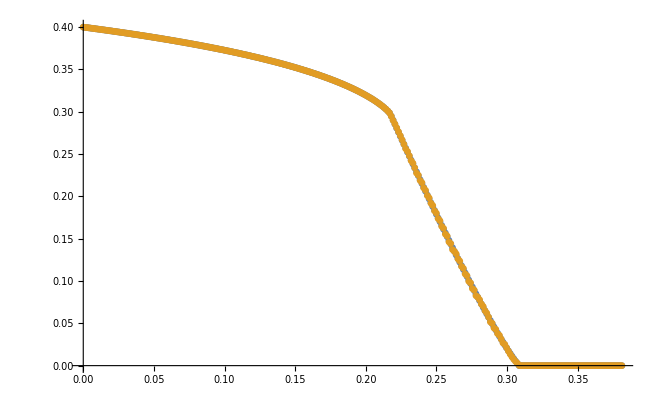

```mathematica
ListPlot[{DriveHeExpBench, DriveHeExp, meandrivehe, meandriveheMC}]
ListPlot[{DrivePnExpBench, DrivePnExp}]
```

```mathematica
(*Analytic moments*)
```

```mathematica
(*expectedDrivePn2 = ParallelTable[{xlist[[ix]],(*Quiet[analyticProfileDriveUncertainty[xlist[[ix]],f, DrivePars,1]]*)},{ix, 1, Nevalpoints}];*)

(*stdAllPnp = Table[{xlistpython[[ix]],expectedAllPn[[ix,2]]+Sqrt[varianceAllPn[[ix,2]]] },{ix, 1, Nevalpointspython}];

stdAllPnm = Table[{xlistpython[[ix]], expectedAllPn[[ix,2]]-Sqrt[varianceAllPn[[ix,2]]]},{ix, 1, Nevalpointspython}];
expectedDrivePn = ParallelTable[{xlistpython[[ix]],Quiet[analyticProfileDriveUncertainty[xlistpython[[ix]],tval, DrivePars]]},{ix, 1, Nevalpointspython}];
expectedDriveHe = ParallelTable[{xlistpython[[ix]],Quiet[analyticprofileDriveHe[xlistpython[[ix]],tval, DrivePars]]},{ix, 1, Nevalpointspython}];*)
```

```mathematica
(*expectedAllPn = ParallelTable[{xlistpython[[ix]],Quiet[tempNthMomentPn[xlistpython[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpointspython}];*)
```

$Aborted

```mathematica
(*varianceAllPn = ParallelTable[{xlistpython[[ix]],Quiet[tempNthMomentPn[xlistpython[[ix]],tval, AllPars,2]-expectedAllPn[[ix,2]]^2]},{ix, 1, Nevalpointspython}];*)
```

$Aborted

```mathematica
(*stdAllPn = Table[{xlistpython[[ix]],Sqrt[varianceAllPn[[ix,2]]] },{ix, 1, Nevalpointspython}];*)
```

NIntegrate::inumr: The integrand (0.4+0.04 xx1) Tsol2[0.] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
(*Print[RMSE[DrivePnExp[[;;,2]], expectedDrivePn[[;;,2]]], "RMSE DRIVE Pn"]
Print[RMSE[DriveHeExp[[;;,2]], expectedDriveHe[[;;,2]]], "RMSE DRIVE He"]
Print[RMSE[AllPnExp[[;;,2]], expectedAllPn[[;;,2]]], "RMSE ALL Pn"]*)
```

```mathematica
line = (-T0+((x^2*(cv+a4*x4)*(a2*ix2+κ0val)*(a3*x3+ρ0val)^2)/(t*ξmaxn72^2*ω^2))^(1/mh))/a1/.DrivePars/.{x3->0, ix2->0, x->0.1, t->tval}
```

0.916973

```mathematica
(*ListPlot[{expectedAllPn, stdAllPnp, stdAllPnm, expectedDrivePn,DrivePnExp,AllPnExp }, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]
ListPlot[}, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]*)


Manipulate[Plot[Tsol2[ ξfunc[AAfunc[AllPars,x, x2, x3, x4], xx,tval]]Exp[-x^2/2](T0val+T0val/10 x)HBasis[0,x],{x,-10,10}, PlotRange->All],{xx,0,1},{x2,-10,10},{x3,-10,10},{x4,-10,10}]
```

```mathematica
(*ListPlot[{expectedAllPn, stdAllPnp, stdAllPnm, expectedDrivePn,DrivePnExp,AllPnExp }, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]
ListPlot[}, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]*)



Manipulate[Plot[Tsol2[ ξfunc[AAfunc[DrivePars,x, x2, x3, x4], xx,tval]](T0val+T0val/10 x)Basis[15,x],{x,-1,1}, PlotRange->All],{xx,0,0.304789},{x2,-1,1},{x3,-1,1},{x4,-1,1}]
```

```mathematica
Plot[(2*MM+1)/2 Tsol2[ ξfunc[AAfunc[DrivePars,(b-a)/2 z + (a+b)/2, 0, 0, 0], 0.3047890582966048,tval]](T0val+T0val/10 ((b-a)/2 z + (a+b)/2))Basis[MM,z],{z,-1,1}]
```

```mathematica
tval
```

0.6

```mathematica
x
```

```mathematica
0.3047890582966048
```

```mathematica
xx
```

xx

LessEqual::nord: Invalid comparison with 0.0195887+0.0195887 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

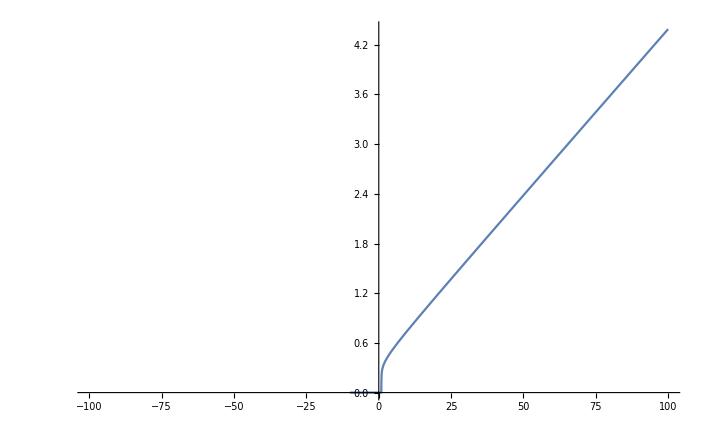

```mathematica
Plot[Tsol2[ ξfunc[AAfunc[DrivePars,z, 0, 0, 0], 0.3047890582966048,tval]](T0val+T0val/10z),{z,-100,100}]
```

```mathematica
Tsol2[ ξfunc[AAfunc[DrivePars,1, 0, 0, 0], 0.3047890582966048,tval]](T0val+T0val/10 )Basis[6,1]
```

0.228358

```mathematica
b = 1; 
a = line-0.005;
(*z =( a+b-2x)/(a-b);*)
```

```mathematica
MM = 0;(2*MM+1)/2 NIntegrate[Tsol2[ ξfunc[AAfunc[DrivePars,x, 0, 0, 0], 0.3047890582966048,tval]](T0val+T0val/10 x)Basis[MM,x],{x,0.9169715111162073,1}]
(2*MM+1)/2 NIntegrate[Tsol2[ ξfunc[AAfunc[DrivePars,(b-a)/2 z + (a+b)/2, 0, 0, 0], 0.3047890582966048,tval]](T0val+T0val/10 ((b-a)/2 z + (a+b)/2))Basis[MM,z],{z,-1,1}]
```

0.00819368

0.0903526

```mathematica
Clear[convergelist]
```

```mathematica
convergelist = Table[{j,0},{j,0,39}];
```

```mathematica
convergelist[[2]][[2]]
```

0.0210031

```mathematica
For[IM=0, IM<=40, IM ++,
convergelist[[IM]][[2]]=Abs[(2*IM+1)/2 NIntegrate[Tsol2[ ξfunc[AAfunc[DrivePars,(b-a)/2 z + (a+b)/2, 0, 0, 0], 0.3,tval]](T0val+T0val/10 ((b-a)/2 z + (a+b)/2))Basis[IM,z],{z,-1,1}]]]
```

Set::partd: Part specification convergelist⟦IM,2⟧ is longer than depth of object.

```mathematica
Clear[z]
```

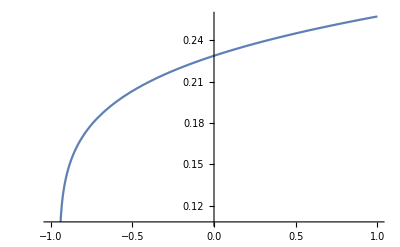

```mathematica
Plot[Tsol2[ ξfunc[AAfunc[DrivePars,(b-a)/2 z + (a+b)/2, 0, 0, 0], 0.3,tval]](T0val+T0val/10 ((b-a)/2 z + (a+b)/2))Basis[0,z],{z,-1,1}]
```

```mathematica
Tsol2[ ξfunc[AAfunc[DrivePars,(b-a)/2 z + (a+b)/2, 0, 0, 0], 0.3,tval]](T0val+T0val/10 ((b-a)/2 z + (a+b)/2))Basis[0,z]/.z->-1
```

0.

```mathematica
z
```

z

-6.6658

```mathematica
convergelist
```

{{0,0.0636398},{1,0.0405415},{2,0.0353678},{3,0.0322692},{4,0.0288735},{5,0.0245905},{6,0.0194068},{7,0.0135687},{8,0.00745221},{9,0.00148644},{10,0.00390428},{11,0.00834679},{12,0.0115555},{13,0.0133579},{14,0.0137075},{15,0.0126851},{16,0.0104872},{17,0.00740468},{18,0.00379195},{19,0.0000330291},{20,0.00349566},{21,0.00645997},{22,0.00859754},{23,0.00973969},{24,0.00982343},{25,0.00889292},{26,0.00709149},{27,0.00464183},{28,0.00182245},{29,0.00106309},{30,0.00371623},{31,0.00587574},{32,0.00733571},{33,0.00797772},{34,0.00776138},{35,0.0067445},{36,0.00505555},{37,0.00288509},{38,0.000727595},{39,0.0233416}}

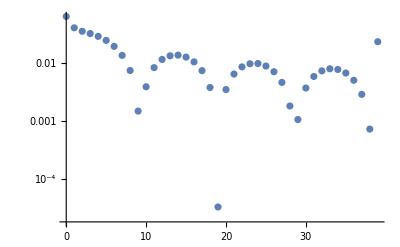

```mathematica
ListLogPlot[convergelist]
```

```mathematica
DrivePnCC[[index]][[7,1, 1, 1]]
```

0.0404835

```mathematica
line = (-T0+((xeval^2*(cv+a4*0)*(a2*ix2+κ0val)*(a3*x3+ρ0val)^2)/(t*ξmaxn72^2*ω^2))^(1/mh))/a1/.AllPars/.{x3->0, ix2->0, t->tval}/.xeval->0.3
```

0.81862

```mathematica
FortranForm[N[line]]
```

24.999999999999996*(-0.4 + 0.8610328431001736*(xeval**2)**0.2857142857142857)